## Scientific Programming 1

Using Mathematica as a calculator

```mathematica
1000!
```

402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
N[π,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
N[Sin[2017 2^(1/5)],40]
```

-0.9999999999999999785677712610609832590685

```mathematica
N[(4034 2^(1/5))/(1475π),40]
```

1.000000000002825769728299060506259313476

```mathematica
TrigReduce[Sin[θ]^27]
```

1/67108864(20058300 Sin[θ]-17383860 Sin[3 θ]+13037895 Sin[5 θ]-8436285 Sin[7 θ]+4686825 Sin[9 θ]-2220075 Sin[11 θ]+888030 Sin[13 θ]-296010 Sin[15 θ]+80730 Sin[17 θ]-17550 Sin[19 θ]+2925 Sin[21 θ]-351 Sin[23 θ]+27 Sin[25 θ]-Sin[27 θ])

```mathematica
2^100+1
```

1267650600228229401496703205377

```mathematica
FactorInteger[%]
```

{{17,1},{401,1},{61681,1},{340801,1},{2787601,1},{3173389601,1}}

```mathematica
int=∫1/(1-x^5)ⅆx
```

1/20 (2 √(2 (5+√5)) ArcTan[(1-√5+4 x)/(√(2 (5+√5)))]+2 √(10-2 √5) ArcTan[(1+√5+4 x)/(√(10-2 √5))]-4 Log[1-x]-(-1+√5) Log[1-1/2 (-1+√5) x+x^2]+(1+√5) Log[1+1/2 (1+√5) x+x^2])

```mathematica
int//TraditionalForm
```

1/20 (-(√5-1) log(x^2-1/2 (√5-1) x+1)+(1+√5) log(x^2+1/2 (1+√5) x+1)-4 log(1-x)+2 √(2 (5+√5)) tan^-1((4 x-√5+1)/(√(2 (5+√5))))+2 √(10-2 √5) tan^-1((4 x+√5+1)/(√(10-2 √5))))

```mathematica
%//TeXForm
```

\frac{1}{20} \left(-\left(\sqrt{5}-1\right) \log \left(x^2-\frac{1}{2} \left(\sqrt{5}-1\right)
   x+1\right)+\left(1+\sqrt{5}\right) \log \left(x^2+\frac{1}{2} \left(1+\sqrt{5}\right)
   x+1\right)-4 \log (1-x)+2 \sqrt{2 \left(5+\sqrt{5}\right)} \tan ^{-1}\left(\frac{4
   x-\sqrt{5}+1}{\sqrt{2 \left(5+\sqrt{5}\right)}}\right)+2 \sqrt{10-2 \sqrt{5}} \tan
   ^{-1}\left(\frac{4 x+\sqrt{5}+1}{\sqrt{10-2 \sqrt{5}}}\right)\right)

```mathematica
D[int, x]
```

1/20 (4/(1-x)-((-1+√5) (1/2 (1-√5)+2 x))/(1-1/2 (-1+√5) x+x^2)+((1+√5) (1/2 (1+√5)+2 x))/(1+1/2 (1+√5) x+x^2)+8/(1+(1-√5+4 x)^2/(2 (5+√5)))+8/(1+(1+√5+4 x)^2/(10-2 √5)))

```mathematica
Simplify[%]
```

1/(1-x^5)

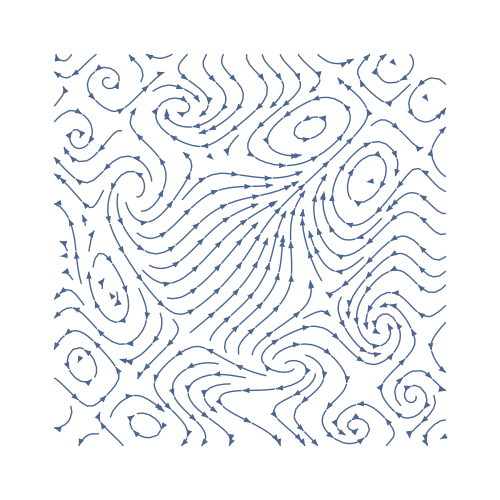

```mathematica
strm=
StreamPlot[{Cos[-1-x+y^2], Sin[1+x^2-y]},{x,-3,3},{y,-3,3}, 
                      Frame->None ,ImageSize->500]
```

```mathematica
Plot3D[Sin[-1-x+y^2],{x,-3,3},{y,-3,3},
              PlotPoints->100,
              PlotStyle->Texture[strm],
              Mesh->None,
              BoxRatios->{1, 1, 0.5},
              ImageSize->600
                ]
```

-Graphics3D-

```mathematica
positions=ProteinData["KLKB1","AtomPositions","Residue"];
```

```mathematica
Length[positions⟦All,2⟧]
```

238

```mathematica
Take[positions⟦All,2⟧,10]//Column
```

{3817.8,3403.5,490.7}
{3480.6,3281.,358.}
{3287.7,3517.6,123.4}
{3571.8,3772.1,100.7}
{3751.7,3938.1,-192.8}
{4115.8,4022.2,-280.2}
{4289.5,4297.6,-82.8}
{4524.5,4558.8,-237.6}
{4879.9,4667.8,-152.6}
{4889.1,4886.9,161.8}

```mathematica
Graphics3D[
Tube[
BezierCurve[positions⟦All,2⟧], 80],
ImageSize->Large
                       ]
```

-Graphics3D-

```mathematica
lena=Import["ExampleData/lena.tif"]
```

-Graphics-

Everything is an expression

```mathematica
{a,b,c}//FullForm
```

List[a,b,c]

```mathematica
a+b//FullForm
```

Plus[a,b]

```mathematica
a b//FullForm
```

Times[a,b]

```mathematica
1/2//FullForm
```

Rational[1,2]

```mathematica
FullForm/@{(2π)/5,(2π)/5.0}
```

{Times[Rational[2,5],Pi],1.25664}

```mathematica
Sin/@{(2π)/5,(2π)/5.0}
```

{√(5/8+(√5)/8),0.951057}

```mathematica
a x^2+ b x + c//FullForm
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

```mathematica
Series[Exp[Sin[x]],{x,0,10}]
```

1+x+x^2/2-x^4/8-x^5/15-x^6/240+x^7/90+(31 x^8)/5760+x^9/5670-(2951 x^10)/3628800+O[x]^11

```mathematica
FullForm[%]
```

SeriesData[x,0,List[1,1,Rational[1,2],0,Rational[-1,8],Rational[-1,15],Rational[-1,240],Rational[1,90],Rational[31,5760],Rational[1,5670],Rational[-2951,3628800]],0,11,1]

```mathematica
%⟦3⟧
```

{1,1,1/2,0,-1/8,-1/15,-1/240,1/90,31/5760,1/5670,-2951/3628800}

```mathematica
Head/@{a+b, a b,π,2,2.0,1/2,2+ⅈ,lena}
```

{Plus,Times,Symbol,Integer,Real,Rational,Complex,Image}

```mathematica
c=a+1/2
```

1/2+a

```mathematica
AtomQ[c]
```

False

```mathematica
c//FullForm
```

Plus[Rational[1,2],a]

```mathematica
c⟦1⟧
```

1/2

```mathematica
AtomQ[%]
```

True

```mathematica
c⟦1,1⟧
```

Part::partd: Part specification (1/2+a)⟦1,1⟧ is longer than depth of object.

(1/2+a)⟦1,1⟧

```mathematica
Clear[c]
```

```mathematica
AtomQ["this is an atom"]
```

True

```mathematica
"this is an atom"⟦1⟧
```

Part::partd: Part specification this is an atom⟦1⟧ is longer than depth of object.

this is an atom⟦1⟧

```mathematica
"this is an atom"⟦0⟧
```

String

```mathematica
N[π]
```

3.14159

```mathematica
AtomQ[%]
```

True

```mathematica
?AtomQ
```

AtomQ[expr] yields True if expr is an expression which cannot be divided into subexpressions, and yields False otherwise.

```mathematica
Clear[c]
```

```mathematica
Append[{a,b},c]
```

{a,b,c}

```mathematica
Append[f[a,b],c]
```

f[a,b,c]

```mathematica
Head[%]
```

f

```mathematica
lena
```

-Graphics-

```mathematica
Blur[lena,5]
```

-Graphics-

```mathematica
lena//FullForm
```

Assignments

```mathematica
r1=RandomReal[]
```

0.575343

```mathematica
r2:=RandomReal[]
```

```mathematica
Table[r1,{5}]
```

{0.575343,0.575343,0.575343,0.575343,0.575343}

```mathematica
Table[r2,{5}]
```

{0.933111,0.588864,0.16503,0.886303,0.2901}

```mathematica
r1
```

0.575343

```mathematica
r2
```

0.996015

```mathematica
Clear[a,b,c]
```

```mathematica
Clear[r1,r2]
```

```mathematica
fib[n_]:=0/;n≤0
fib[1]=1;
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib[2]
```

1

```mathematica
fib[3]
```

2

```mathematica
fib[20]
```

6765

```mathematica
fib[30]//Timing
```

{2.87651,832040}

```mathematica
fib[31]//Timing
```

{4.58299,1346269}

```mathematica
Remove[fib]
```

```mathematica
fib[n_]:=0/;n≤0
fib[1]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

```mathematica
fib[30]//Timing
```

{0.000182,832040}

```mathematica
fib[50]
```

12586269025

```mathematica
?fib
```

Global`fib

fib[1]=1
 
fib[2]=1
 
fib[3]=2
 
fib[4]=3
 
fib[5]=5
 
fib[6]=8
 
fib[7]=13
 
fib[8]=21
 
fib[9]=34
 
fib[10]=55
 
fib[11]=89
 
fib[12]=144
 
fib[13]=233
 
fib[14]=377
 
fib[15]=610
 
fib[16]=987
 
fib[17]=1597
 
fib[18]=2584
 
fib[19]=4181
 
fib[20]=6765
 
fib[21]=10946
 
fib[22]=17711
 
fib[23]=28657
 
fib[24]=46368
 
fib[25]=75025
 
fib[26]=121393
 
fib[27]=196418
 
fib[28]=317811
 
fib[29]=514229
 
fib[30]=832040
 
fib[31]=1346269
 
fib[32]=2178309
 
fib[33]=3524578
 
fib[34]=5702887
 
fib[35]=9227465
 
fib[36]=14930352
 
fib[37]=24157817
 
fib[38]=39088169
 
fib[39]=63245986
 
fib[40]=102334155
 
fib[41]=165580141
 
fib[42]=267914296
 
fib[43]=433494437
 
fib[44]=701408733
 
fib[45]=1134903170
 
fib[46]=1836311903
 
fib[47]=2971215073
 
fib[48]=4807526976
 
fib[49]=7778742049
 
fib[50]=12586269025
 
fib[n_]:=0/;n≤0
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
m={{1,1},{1,0}};
```

```mathematica
f[n_]:=MatrixPower[m,n]⟦1,2⟧
```

```mathematica
f[50]
```

12586269025

```mathematica
f[10^6]
```

19532821287077577316320149475962563324435429965918733969534051945716252578870156947666419876341501461288795243352202360846255109120195602337440154381151966361569199621256428943033701138278006380027674115279274666698655783793188228320612714975832303348548934895725992307229129019282092643316275217308614600179125820426996599360209593392020051848620284024473431398113674187202038684801753185386211128781082406177413832935545616876064540651259547180291265479428940369816592063610193592913521354103767990829403201557027161153950319759732477821629576316296533566947776632850623452455934606475750259358134434578167676462587885901137272990737294785114480895724561915035070255895291168685500088020132334587472177947814475467920160901706425856293597475465327575757400774320349134287851897953543047345603077650789387672865391667992328174493619915237681495576320853710478597061884387315305823956275608790631078190049751695947097367138917457045552021351233507944033607120305041446852210415650373210679322756258647511914611417360349681217380234224786080292021093192496490409832397066832470544417635125267324552754195016838452060230073949598542792982978312043821157576457876924955833514025221527206624418090032593807536284917966809529711850719137983367887377045991363933395581421203699026161797211325091840023055327607104316478190974300434647793363287601469996128023925829471557316688943339455429292871877487747892042961663565366107960239197021097284729667094273345863447980486339446352116549715072613427682054793209317507988801013041602798250635418234403455874223670128266635693461129461312312838906003654732766024569315151850018328483150645480029978935985161237074046158229354440701748339514575869547491750264542126364262224720600488554625899611904758921012242805428986215946466624785643735722177755498760876859120301185516356689020103446399839773266388890365078416180709154525299275973521395741547772914600879431433915606044582510782351166271892637923313014643880597879468444879060576786297460989627426663569682474293386740207436559426057944790711930522589315907193865455258804291397471401818491697338381384461548430631236492908355842780784561319364575591172213694633818031160030789621166865289595377843646440238251636244971819738544414956313171400285033892822274134603018094224837216321854717270452813824078425638747365249141118080783866506339945376239206700513391873331071360696981896282847632454232993062728704579912932457411675339022744999630965666809222625164685825445578513498241441272612401581575381809846666714500698883917855180089437018902572199248520874291556026191775228124660628996787166529678487268484905041328497297712688011639978376434280202452251550102240354169885185375015846738811940476197206196031265344967599178932444781707029044465895719502288091577938976424237518140209989995816123147790229578110016867018673861986179713813985466628196954855374070735622861616553942807641840809212047932816683005984504787929406356318097479755152035094682765918741610907637506902765294367561539803261388901944859410045292275418809457356207954218996629634413463969559809913750100537602594401136172191768811472647135498087560233984759011932754738925753084798049073358372367268170337326650466293577654655686956446137237206007272970374756751781604380114131844687870911594979938777781128264326798279051570834173895471133031409372436803880906566595766787075514018743719768827874371468730850359271665549721196784130412650383973567296441072675534867583350405142738245998707414685317897838502526496656325426833507169940199189676117784765028788679334506639170422673773246857633621190971175445916219735440612809994162559376843478887835657527774019727918513993830659000183040333701319368945967228872860733043459136583011338233204130753618234450087661457072523768694579629736468411076297289773202785082828195507544630846848475614381175736950145150613568790195540170045947861126027141658551071088345832529082512441105583375897863704748059860453472515002576209591084137302113274084462022683663213353775766378946313883274691172320590295400249563180463962904282511861823069631606413805768566669887175825733183772626866700352264675453451098670176158920724564681466379040482539781408925913175892496646873486705631883193817545825928711969042296020593122261312832308397380320697475782326926053089803117700339175622833079636022878074828990936449684079165607521124185121357011494106314604057388041694756710022316460900537114702107843824390119835179001398257490296445050281525127250892130240862522693038168620273414718216156545123737064349113430883889850229638173175753146504106383861733729843188195339335336422986359916889036204117868543826798712986683052621123913878725711808354320132081283462860456188900899601857681067764060041206892228733050007268703812017629122625174148602209091587019278541185007110110948073032156270509275156383949764826117579719162060093515954412129389122423843836521385907076938747818598648961410132463700675457719970781802401938051763343680816656390378301005573606506402411583703083367521602548032920856128677323133733623794249222948646769255675582510082542731697796399173023320969866535911843612180992984165461621231456044704709851970488982195754122408484430431491947020914293848847005014091351477163750465039879365139122322975356679688686607309936448710011827024346701515293914443313082525027131273969844166806703170929367543705403502999906074781067717930123916380180347981940855924023118494881276803714051624334119261781419796030211868955123277401243785470662133245830166075037988621636926561326802921156544795730058589912408903987073678681602474336901548278508688694000572206826164500210989598907700306090410050620588150196997459168362808231108618529429700616082103280758914076323989760370490897583646216117942955868556789655060405033201294649659162972098935072487426583547183554893834362382683027261391459804683447820578745317784833002937618309028920627335819276363353000960944334206013318790983354723911941475441247732915646148560842439512600507960500976384006973642399124879224985501650736970596699620737469162723011407852512134136404264361205459217481822659775475887871576449973889045227199530567088413439341640459264765471377410467325758511555351607047989570470051031947704811185283699859483563175142378151957939359021464769229769305342995712046209948535535809178192319846268597639266642348134192443088252336345215196896433254512041433531641934079232856234992947398757207370582426056935826222604770315685258560219881427081247798675089410305480337787381222570790421531557085624483556442893915267627292343902087150071599564528146503541159447689796260910868490306046867047415359591753526449950592391971500657315152136942204283404241976033805212729390513346307430964069204937782597954222292822046953267373341633666858884645707996639584255020761023933111981405571726833349548529626786949017605413011750847009009750867278596843438297631820231924418799454522134009862200104136970214346334283001737480266605361624054207669073870417230047808745914430008416374397456627900795807599264543387138394543634400834346482641720743526604228410985636181020232677651483947894203365961369274520742057602073449747644976017294371967560216536789473872182777221675063261133604879192963575090789683905096256833029228840056316421691353529726464136042063904527578327411071959813216206422039588226486951763832235329234801161088131126110627126768503508728385476402666093443296934809989671667836759524374521441984448175817202349208255067791489207515836875157192596112437298314705649836231024852287819286995967594699820129185812218893384140805254655722155162074200656494866170768106340328552080962736995604867477416863836160552651840281914266633207017784410232366449260208163723289932768849086897087455901247050366710191801625285813312865597398408146967225578322237221008369823724810801701502552414659123888782719271015241494238142097336183780160615527079899755242253877823574838633722389675126100481979503656390001966921225298825053707463577721409963345249306902797142637355729786696103181924064929014879859823698251210941243604977424081311919747146820089972044784662354483098072919727134248359742000141210790512272607545793569747119369740025702639644852886646897668469047722085373795350484170327735814242215608024951592025328117483681291005771672871823404200932279892203154293354665763986678884236640253460478081377253289679941566089126066160665059676769689809422861414719951460853012335197017608571745603021793935477496677909431455375826333240794712978963726284696856867812785367444458582928650492831303328273869597484296398887291698010635535948384180709526854277282951652925364366489085006189329090227070932007672797131397118516172543653291844538594293012950757678265170331381013864461898950263792943350669105343381275505184471848272339218088194479150576898067455513181781442747309525171675712234873312398126192348545242117513083159200827006221576637913424361565343234933617458123834079320424775237839421253474372583854417860026599779016390446555142364809853536777856758108774102478101131158845753165207058284840622184940249901494988174748347156008793203007912646199474538401598458386480755563979675664965698565688348428291612495185492835844928187327514938318234972375725445572814053803690612314056825542803287546432402794146612889642395407132594540016033922048782674279314508748147188464655317445240455293730594878762362977301997225319760734656087036477702239506823719190951722610756230575201260314376821926242743756757648915406624267665496118653683057883637121552442708112473893497797581500868741858398234646901949154504838739579637698958457478209224202505650923346097336955280588636665432126073146997315896233834417136714226478797575974778337571284915933140599829590553605427794907424795807597825708942857162001975829946273804093031811207581712325762868552650674410567172505451587691855805247572354750160688939324356696765389811271744739152302409627425992944754147635793320275767817343023843039081547114199183077685987075408373214161470787997803785156176137540031377906230425296895917082401819515977729111581600783799692571368512687500759690052023056741571294471499992013799301505123176186874347152234084046070295532950058491204911395548472242446178038719988141098521899414872599790350053380781575156712625243591087138504440728672767146113565284580638373320683171248800914798556063000814881951693894412767176544893086290847787297320039904401426048032433105831426065071002940908396423007919460944688356737769593361623240957317412681799526236585636752506102364485527551490728919098181736875085621543713958569462579635511373166144733581050372423790956012730888988126241092345867231776187568964559559493693419174377216985475013378102936987343113111650174173980163298364750521273498779032395177050489157397372200583074959792936112841973072792608558696696631911652784237371680116041341610275421030048412695019435298417903190172318972642428637967169909030635532572951696776963774050940986535866663260579835379660177638050218379908418095404354259328256869543425889636385249319903620082186533902716881472378858539901562274997367050493217222198063734171936919041899005795138057167440869419345414080701204726094480024222755388369585720281827299346832771742379260496899003881191900094986997174394148588628262248653850480004275896571557388600787958075314102690314856808827632084237054213435479886958257382372459296580475109264358567793309861569419867302355666247973111904160681169913637566543526883415978967585613712360992907999179828778435773257067909387273925444603755290214928891719459969737162932396408224904386192223282178152834694789119732217147927054725793051687779405765180398818543858058859217503381046522587060736373933592177560884915260622118973088888155068350889897096605632963592336253119105083145031641783341540370370912793766996353124026043365652822002261419467613223333204661830504816556994688777322663682257631958470456369792465220016948829658555113628515643765153564982272437505516998192972989891158551059047147616322662482461189516934898673979407596916979624954823806387790338002833725053288993800516909782342331262412499335822345640468349550661368987412827680029783405825256835967743928748335830691728703998562635463340828100689084703976206414821817408736947199105874719738918144301779590743338296090546423109871518623785129180369966547168061982355728732049440535967290510852088346639929977857619421482101950335404414241939675768045652469707466543792702464292481809810384952601580425138896021787118667251867113321692078057609886442218021299467854704651386278005425001854708809780116567359730935616689814784456346091475765704210287969960108219836243521735365379579784176614195974104335459870737515446202485060040024256499463841767274789013746023580474280911248428689777010427030237842572967215640947079594017293121739599490047165364683043750948950104944970072442236624487933438370818900648296019386730580996814896490426743935484275646157671392564524021842367803968803679400179011304959508510685679605431930709738906345693680915279193509582247741450400892483825154006950486506329629063215496612899735898556153229100904068445249388577143447919255217524731461436910739385086175958419649219105168741799282774726366240921064779689264048975313923282695913621159037633030541515317717920738217522942753488081527148005112835968823924537677691428004870842127378277477867484081770497066744703099587509859835949007421431985601892206572450607581412431060485856741838754165711833791083629569846862595469415736762593489140235974889870026998315497889090475578610331713208265105019755791189401904101795336009342956971807880509074491870630421213685630446861626489884433310639993241749841010375603472835803825784169870258119691174755537263864384920009801833679636517794372041396465909428137680889642029543651780950819611871455638346454063523711470593990657699079602273251837289933171765619964800286900160535914977692772172854077878031210794136551888499610250235974454583997788449828034621820895473251006092511772487845842145190210094112417505990569601355718166688615316200344802072581577030474407302225985493350381189266663353502153589541725659493383109089219489609056920272363989070562270023858591263410965482943836874483033918688298780841895000947133861995743941795022119254484642537181633284140202228339355845226836941906916741620185907172540151119469789094453529958485401445783500669682262293086983530485159408133186708674378370247700857406223270685813865634012833439272185255447453282302751132002160904913115138726603978703776397984852019647268340150088951726380759166566811169826582799248391450872777953242076971339628857294468502462799146322505804758856677473158996439696985773389703021691021913979420112754716503558435228394836202492796848035755507765392354163270352650544014605512467349948693828110999901686592460782161338448682579904178982956863442447182309116826990472258624767650908052905627700552984628050421920295747241251545833213707448645179964069739724593528657550452025145720242619004798851592128443497386324353885246283458678870199265843479269809594321844551765192842509746961019075635379961616953985601203034965491950309543341346125929144574175808832827840334451695611398940716715666420233237282161003878262006081636680720505091443915556178986928532992562966106304409634569554668720543834527947193772712178554684430921970633962942852578200654758262913739465896701560181502635422282725115126804113746349883930969128690609335458900957050829127278412796359724790317315399998567317460885254444715295585634396797929004410788420752930270708847078753585200019212616440350269177573936083767614913475140835471596784414550715461884662569363139506021061100259778914476862706751631265769648279411768082270556609776740942160225162271732635498104919300371876819367809937794707206431212970078575081730776137031603740225023213424808575960431694507612025228437932061767341871076227432755735996865147439240777002698324835122079871759022821245061524742038934446498024987876660034681929840515800888129765697892839912686036610984065336042259161361007850667248524869823324499612822042268257996981471503020843968783976782899398007428473525798781564131686220300626016450047943425210523812140155323192689675777458587366439003474008608232813910673559100925920908121704227182581817382744480499517606322590859276791085240996730730381356337371556867616226666837338074329600051614859821530047860280919335973194955429586708867803958596750463136582424905289152612026908481279462916821112344747410457730273518844234267229877728952331119257871155595764813946967669390191344232336190530236197741894531920362565963202710465592704798144212032397192357364082297924837659731907526505252940276774935318297306652869981404604158052313094891991350884558290858200300446652585066075141579441063491526740012722181493444607191183892069517867022565653247722183800322961180684057578196763863943697138038181127769780676469288297635488951584161027206117474716227214602110247897721796238698336616123723843598756758115523117576612192860179359448226833364954587152303996772565742643025019941531725597536619952189050276390780211368305560983699616590654715919708451930123652859887859953005741271911068846848476451607855153340423402168058258251385693333675669779339066406603280360061358800980649593543071678043423774167623075939211392012080337222912036281619205773587371742600778478843417705003864951541572207937899175038239504706501377035542138411652633747437801216804599003241069907982880972508590939704873646619422760350321477968293917544482070260326678743594379267605778522858577053541040754946922547827404227135781120648787860967654270901676773036318720427226941597451665689969928791190759789037196631457215341254311371471512051809224650146698742741413699420106697912559258909209325096612512328794262868060692455960117657064762397936006021629684672694271428754676763077548152563163634899817302728133851939683846810099123052677337796694856075312164771254216946472372080102817023001292963374996469587711982351783843674653427495809893467896995099347923816665581450094674493931687645590934681523861638083361498669688820960378159397608206121826470550027165749646307804303703893042196604966559202557073738547312374284251549655655201738653950375706632918697318448654048237816231441614288876740595492554381280750081561479554340407393633967517271706220855268912514253078189621816018760785705012203556398079125543001636467773459922914537661648874136540504710769342904110363034790377520592882355983398384247457271915029453629284168686457167958327996202012838708705661039048508843776792516917016182821872828587217891518575205268031306165587626888689483150951534735697676587498710211232883604406475635560522532104700044108396080501925286992973693732723783398145024598374625361524779141917057615519399786743860135794414878274931770896962579496476076403622291130543844519502419138254910041763897829928389227696342650318153224703155217130435641554361506069022634007510317736895282557422998736504850303814478948576263995168029970123605999164140777869508547476060106958847334554900373212933510283755038621203679508381502251048089027378338794822710816848219051517160593763123173781779353275780788332542727273766457279831300455055543778307678883669056820792417125695917442456746042853323970626184028190777627557079589080768358880710304675136619528382813023422341900183643691565505935300641340426675577158070357264506466072125589407515687503606243399440968684597968135194779047653980135273843794197862277213180674990420560040187575618982273181271043865823417551615233847258336965003944128318328992842507688939565016724214963639252425822026187302172512361384769534827850804713101816314798008202746841979426112128717053542178042730711404827442102944587712442047656992296252334539007574455314383740787648048809094303698171865886662885674979865165891370909199891173175284881958359967945354771627889586512729867344696950520487778678858194187751724140101740951138055953726846172328685801316194357831217197772845079166391096973240899071428799728206323581674158736320825803331664226799638238272600310688864625698878891513452386926268145285448710180872820720506346062536070217837734752627566358774734069108357047822708713655315738407194413777923568770661271636798205444523209980812326909710373199781797808960569209367574592631281295536462408934702954703363444449688814827345893433334311302667484013445171185747261715772188811588901664583189896222653354649433023745964066539673585011302303430960639281466001904820015520532712093119882646505917801398364690590391289158159401433782241061027526871939382511203952625724480638086611299185631620345522289618540246234933003923772444755247418985421517126741293823302220730147045377798763299993021175193229348826837924782822199418580189269710055428437524697839440225495439684058966478319776885882142502882888687224977598364522933192057820874315946553981699390542581385245628708673844796740402623232201501967495093026408968291769200931924148671242196527371664668850423871301969851548802744446200956540503011008371856896899093325079010972715066118124457792077930253718182660196188949885351785782270536946874537273562206189754822221624481995029235197986425592858793647141654237674638717303935912105920811107134482026021814623736446170857498202734422155489119523715254750999145157685219032510592768402937566635739699827773390881414532759654735559894645478729755086480781089436181006172360463808998120896378832057068624326036890770092398100637598811712518265905958813605353847230689702535883375183111732325045886135899421411809069635414125412365782721408256917043623428744563135060416906896701292577201555903548244292237625406252577860867468228241773070870048357136384276145438595709400401345875882427215560027590881008015349440028784742867853667105895576460733812792517458606997772417444224366047241207544933851799320463271548497902660458720133552653072688363280324291553017347080837945968498270752816056723671956358312921631679677247430819274156054574633697227918665019807281729069856947325610556388172387552950538148022890007861468150497867896690799807816743085948886655685063668992568118843586736420275799919706667080916564967160254333609467834712530429270850847754598279270246083121141576760105013339223082477672643163056327757911829341529498122069608533317436666386585124344383885950780050551319155599661698216490669248132440671458227151421888803693314694708400874957514275351039996866800432884101443720497483881526933991668211118402225301598273775559541374392055105239941878113239572706772961236337090951992812581645459796744411288540209924619182050951472962086499214880164028980020011548891879863320034257459422840347414300262733208897639052290009006077874172595021622378623938183810392911489202674916783172995013589163863932764298547738114958913203074426161246107015334655586449600827966205355476110572440765410218967011351850431845525561250392975797039490507287016235593335472249354805997114488215477819865576130783286420393499013074976459668668252364271146654386687926231506682369660291500538430768300687714635841592999635395700724653004603126196744813000316366727889817798162519840442535476324661456502617987670251329296775158377429776994474262540205213211792963145753364668028791474116988811887653352920960637361144442438316641609910902414038844178035891312526217253766029936739172584707371887588553299652932996805715301889693119661966480804011727652912879641342428077599065715175694889257427588917120049557520411015425230417935343122555197530996356965386060689427401453198686978969635502899536809475109190597955206595534718239650988332879893649353217541267218527336402409843925305201859318720376447322395650645277529735873432950251888634855142029762183884660966769652344248627796720572341569275679926651331874679109920251907044788210811556553020166610642327561146290885737746924439075528545968047102439309927828200613548320149727668961597343770424320011823882287770387005064934082504848610532976385610240526540009985395854971901193301814990644759730003937821293240552691875530333364794821470093759967200885146685683995800162935426790713139580744739708303212430756150346220803815177350979081082425545538332678888025863986442161510202766050837987568102621480489000376789910177155592676644761057564632382936702429195679766163668393050137763047922042093987843618233814542161398590353709689664515052196585059722718758802988989895086135047035728030261474133339722886672801494391378541498117879379998484259999496944893699273838166479794856605920915609286889305461291213744749072804466859550429398912169372811583846324115572845110671658615119059724158386211915204001218168561975481969538353435326435302734756548698380541052200733573358026241530162172896835607519552586427771147318672896492975285708574771328188113532148239594950246765780851746632290608260759792769698177240992866235979984815119891653455938574081852747349287585941059640841136798756057181552190118125864838184966350731902457906061335174417453705397321733308047497329505697501693042857089996795435801176846313849817723661491862654073740986047790766828966140493696841763256766171082239865584067835699125712314726249563499735444782367260097574308949493606041581173571905641428264846171690374906515759201718842016547289258674171766384161342420014535043094273571143137256282123222066298226806807456837805290559085667937644725438507057097805179625143268297491876546768704734062081749962221070227762647544988977952224584451993145231524855897413475328884706329178310881030620298963737777150547949055078608766796303840948428493714153703592868152737185772751840445640707523560699447851024211246532752508422777997579644420211941939270429523758973121457657679179458674579162026635480372486466607874200666943079695571147877496880676660585188929609444699942655227026854405657776845822108383312810570629382766407832671309334933971788578967689828916594391731747175627569852370788733508188128928196000900794043792819923452598943992610886838847344394195278607521489792998383113226171663771265651129042877309477726619328416441341658411907204931474330262021100416615675028817047268874750309978635927522618787082608316085423872734420671546902794680358554673033154148555922650777413041389148852156576169003143282279526450203160270293599451356020550540850300567362338594198833244675010968074277628324166150346037764452301950685523594430059034366682468599967535727786409186713162415688827043137950878448384485074393525491363494199246423571519463969178896947303044815394522014816819187588387264210496130834414637040246494505023447130261102089605938271655452794136197219484915797041759823815169019060750382009421128661741750328717385814787461650387015285330964264387363955417743044075236602300325705970211427104389413935778498390342272458776584483187356349860821873120861538229915115339557604806339925700486516155701894220521239320844538323566210308772798739930042054175418243009074482666665098625357940496153055569243063869557481125132891453886695310731643260329551735413256526060096308794582143971225850174318303493639723045670103648898545907527735919210772078029953058447625228149787955767276492352209552036205239102997782599667379687974817776824008988491981842138731971636728453444806364831396680200423153224123482731625385960223026875472778283179227844977824134697524166179177044634962163424166300246170859496594301467557055896473582739773114342730849476663984370913963934058555877976902730576483762507936651095721646653409854567134551475490091746452348065578485400419170282047242914330406448493435581741156887093189374451857824383603312156095438010122145246320506399569349354395504292513460563813990748036792149785518594623780807326100520165933374756831137619812074502800716793088657223232761622113455720110236824790836940569549695468377730094359242481606765093399103541611286539631681202320760200341621458853918681778220888980467556634420652118672711499829446770500454227797023153547148390872174625478730825916293245563009920153098736133572931408195874034984277358687747416252981485334954780210330398939811517716932045788276872122525732353134179349298937401893815801499388812598643582727397627816072896996781107656586481862240055270947301675536703371511250184040678972866404743204294243446561729607214040697514484477988196741648235140232047691399200486653691246676596507321442778521402108993552497323599124328729606309435900019855307963577890663871950776459405371080481457856958816675456318574370373417102137825145240510463323250128772405591910950346755184730034316384098009674960915382846421146642665315894457882365176164131149431813803797899455723792984628193515927322136218573286530183272854303456518690763712068208759132244893758701041751519893280296569057643317460054322464974328323951680955126859310996485130875730422536160339492236090709269743786647635725221585553247188784351265621943902553183569657091041846935985244661860543704782467820474798001829698214883988057993911374976771604696723170569750321686860584217297561688793477274242144042590535938808062248661113745442857046135727565724416669151839047776619503417213085098725239183244731962088047703798299068321179181906729807291213312488533781211577701223183505097343754085409091932398266236712888002782647032404217006370606927378892561980713705442894618447952298044010796624096922398096032548303953848170472291564760423886777289103775517947593647249899341842773088890299418330667810633486094106543980338790929177271344542801275693661497830736970166783589311525899388981423329581284436680354846117259970765236503109571907198488273111618619377843896481331371332504461335362672913038347731792670810712762679271448425876672385591889926214254655489179528725301901240396098148057735051656116400943227634045546792230603855234728286800974993293766190265783922970768106696081356246205687546962431907674546844761676266002082362170628090036809156866376089560901318712756944092061125155864561240821145280084150120958402874752935404354249672268179836266991590518093626587256595873752515454187188680074800632952704382295286911366691878293842539828533356862994930520439062676681913328453601393466338465814993085922425399263930901807654364026560664656446978414181123131590501538116411659198804179978205275829642190690426301480255291305989312205650149412508012300960572217313259450237346376570181852426492395511076824115789219849665067278706144681094154368680193816350571502993453870624105236202129123358070988270688792006809711559462210817284468012751667839744297283230560074839812284358932525391624380762464380168740882453741252924033294822987864430114821603377942901977885435199392583304185851219530038875051381431446014746268071156958018524119857507471979328113627013834829195218838961404656454259888386514254197149109232609389723215554772391100856559435487714911060929479455637505084361395860401789553118712912593901674015789328238706892678729536040223870339645427923612234559114928208483153946225414686847927318057653575204116977020542596602863635535993889201884789481117328186732775471113692314086617018634304110437391021444788080826400274604022844615968764342673340778050391650728342426358368821003703044781102609279837798326615064213716801556680911813611382134787953035739633136203258781515828753787594473074849013680951426139298114031467597019658149906702220608444322261658034198087104640804778252407325333452009764107420213660863665846245230222352108353481603679032535157716196704746268450849692449016812055854132643968555141535584108727663216903801557385609156465472483249806796167158047990624741994274503866686402751643916518229686399069106818704590768467922256288544526540828522590406716505091819222197800554978363426206429085610417819669856210807616782760628218496585276071794873240773639556281960178549979846398460887895496408380207911641285156045638690590576359043712546166977987829113604082820931893884515830548060273651894194445904288365347513236993746270112508984376195531259057391582592439183665533697718467195381410720631356212652680340928887577004118837346322125409458659065396912561510056045444479457765892658215140651116292569831550835256262460086616303547756859894931497377049396720443316082961682665505375967297879665148823283375181355501011873273059734171576090908324232828693393832236266301121656679441302920347349063894239288004725858405745176434318469079907970767212089907127301584929060341058299569393599734730618009507276663875326666490285741351942399258966980155377245171226940628472424626029175823140641859282754510624128341713710119665318729049989124184344185898558080781824031594649698923214535315636373685700465592087236996608992514024338186423716234335088644328052614213375797304166524953739898809265381592817504826101701935825710756729638502217764832513069527627322174754355039186158493066480092023360118152525645110546072653938309036108629703775516455023915698316990404509115342101925805984523606783154907900805711748952716009593206776634740718764280968798593034352192020201605657577629212078448141596856396350476136108288811085308328322058979608200648710797458872656604370189792004028568679330330262434993938377683994412312140252986711693705382441845312112839959610950204585146813749964314992305693245673789491115792938270801804756661997892358588056984447097935129535349868454673254105762610422010610841402324081974110009750662794155269746841155883823524300508495694422563290620128086726306018646835802822228937625895675920276646948345844083077085136429233848173699151897822737282952551387899711465448620858662794229511702153746673128068333805333291102607813613459341375749149111690029587013614131063568323748398974387051148461350740331370308802920589725632490820961835868102247238165014322328288577507963703839584374668802514912291092672861675205824379441455214375618851287759040093609768095470298813164395659291797496536329992489530320053824089270011385652575240822800182309687143237408871343331044298290847302589627145755914618229902934559862610018395512596043362882925720799237493197348885847493053609108033500667532585376303834823106755851223585131810557777389991535350626031292932113792036129413649209561935293149195903179744607447576533332358242526797869279456595689539869257535502633255414572735498102528905761463966726374102538886197560795463480265434370868947085177790065658584131521330870886860396354782658029278130892786476478507495386943900518061633185728476733629516191232320398542158475115979365704013199671449051180281610659179706829141731249863009284457285725703573239798775348850646940522958800126717374590342782974140054112458166101613782024448627665233525729009383971950774893482837753996623606252365601086744129563962761619270802362535609697033269591661385129975104607104481352301024096441623062391760891233319273283765286364683875755067758291541686731018458583145648610653640487049389439110796862218715123242931303220606307478197206189377115578514442821668056281289662641132605751487768684576100999219460816269168962986628459466222310923350514802946177477907824167848354232974190584466014503200743501520606787447937610147245520345971172673745403606320456820149851822346211778719522208803876483632573416225733384376723539826939820576061876099607404094959865138241412402527835195598292806002879480455386374202177338551901978184677958248013629721045436221950646858451417356733916460740694680400643891513632607738729755752233160805104874971497571182675749992719888824580981628970192636416976565726400885024011319090010315129979264549534360760501758122040718607589420586309882801469834317317828914156192264761048497414560960500412280304131929822157972765400668911261230508426962681266293353644688641287945672879514182310109128994604376274088422373148053551404578350001169188483946962416531758534882773425235456601080915050692765158436015786160634863643624058121818724768450675362958530684103812064966134209836078917048640432027602079019009365680452377734779050863438332569424467132147008745325804612921069518906948553764948235119040109337554522799459917826448525914337096425012725541585181594093185044480367817621116395979187652440248770107684280484022181519513036876858204036918325578393018161785908496047444365782925800276621178855338064402271845572666914550121710447233877057217188003707034457159654537404554882122557730956893077793507386227303428012212810706800306588247177283397692004867826082441817499360358303928807043326816989558841558278117205884081672750609525961453588918744789255116049130750974506644766067656577572576671778382890051827233057348533854706066544392099519880874769461884377293924293739402014517695909921442161183513839052636526609387400549366244790068456700447249782705482389533556140607085755888029332138901364969597471106728783394171147466907456653398378979672266386126075330536067245683038987331905502668251628886845683414392084750183039189641899416161618811142348234829911008309152873368957357859667502060327692090497605790220359884620936063697426348098322831643628808683184668577881781169297472788963724466623110017275448602830474503001396944534678898136047664185363023331199007470926808589373353767923249257880585987496020212132104519818569736467797544634945099838458165067580844381881206522895158718680001420880639456593009276414489726597523512339979098456343762231550740638213746492982816575167838261391626605552450777122455755584292768232156003701137928007363343849346309167573952186433286151035158404660880889825547489846079463149696341409002156958091163327920332843188621574551372533939132299837760439696286535379445721804557788315333103853519602634125765832608733348339365283831664301487404308152732419876455804589328790621666188375330733323442544057175395611572780562142683197709432584939379416315642240792375806510595622629020028360337894431366175988843882273342387104257068281399780207049697340944907924949597298027966120968426287744531690450410138738690003102503518566684971366120803122153959533288217801946195991729896656711916200213588601269247235586362455182586548724111187520996534618668435663019606923164111638798741823063855224039985263589909357998265549095775143328153024292224342942741847084925047883398321492599704348871701130038087632057136496155484605764097292152849902175356226126783645870288448247267737676407224036905181775065765152181053887075913788878094011242749300433774583049908615081950844848648302895700565272495894680874905047742305665695993640087008636007677327108001353568965484230848873368390332404305266459792891296057832728244226787511117247008436246231334355815495949072586114063590799162237035171084475158884075739128590394398767201696536096923343635194051449077071676018122119664506706315846552176732850707737058670395086852764025790945293183472784772261673676247141065197339256559940888113210189728707858974255121272640509643963684131011542198436052966456277103108342841222230666347254767648249096681242096421382017002478837786831956768038350048424544883212707461972439779382283978722931417057450899243218922642413652445420504585298488058946614156417854288291437126851161047779253248510349416386508317131933942308980294798174998506973184374136884680901924725555297980167738597190568073350021278364964371917782896713682047684996558811922339811523098669166222187943773508478380880678654046309274414886519556153918996204600995802054640778325631605110624165214418510285185713933189608101346647007954406898828218030701968640934219818042969803781363778729834520515135031225549937983575788436546097988102529479831100714467253341315657852855223615570977726232074170730155690271505085321872928481534934150696552175934029578827625417403836893952335261425791323687058787580527256349447053014833039431331683874035912006417530291688390481216030156309267258007973334967819173146341349958298407413284358718539438449945010830715712679542961017289464834728859956149605652185746140425905037321726373917343202194561820844847303330564241232604208294295238527987335205197006350401862916906051918098539338968828918707161160437555256995772373549010931103333609333269959157417119170138039455564745096786145885958340293082742115676446465333512695921280238661633931999753825245736306547074210012953043803726023420426110292690777681217955896904455330802254801527004119356066047017520452709107503927525363758277821332304028912772252820685838417984118067554728868180576061745078044198551592377422045543303809599966535466088657740493636807264857527315472141941738792868756389373236403722332846357350893116056761991733952642721594462456353895846448556402590759492808239266547557972398080088002292808045207899487314280453337653576065343193754044552024431458101221958867191825270746398908375014901239611299532442072378285173360512655477382956610768419501090426100004764431172434175716406906894803063537326638857350007593339730948625606988230234940911855315734029389149293495611033313781050561473509205538120923445224967818262794616180098333003230313732781557883491312831532091110173699243394434418262216220828776325391907857329644421417545162380712597424052934826439804114971998712348941528730200667153202411626847340652725765304319337668866358797474070064539616921402591572481402695843068268506664300182093766262163131797048730444436342517880848034460140935679617449894104493496478700924485697314354598313991064663459857425037528957268015306332124333677821823881765126752400539125974602001905118110553797737581664920644334051916189037960631904599817038494837401802706376119576716432744487379067931195942282922058257641948792145051168872910449721078867559892477232118474887171745071107731069116699796176481285536752709723214506311140296507856697815773404667203372626276469903139014985902970844365613491837118624380921726137439261972395730218739232479814396808890455578180283501256031525904242773090898420174783992918805675611244239907553915922433572755781697877074787486605443546873812294566452171976468808594461374351783498047800509977742894569805464849297568023892582452757470726446830909893967932551352517631171995121032454700997312047156450475024683469565844172646725944661186034822300144456843890631835266109620075332849056906044400628183859736743738633606502626859568040721492928149002582722231902691508082470287736113193186420147459276786922488452962278871025433607509565099138782208123312862748709668135976173953922305460556328124083314539905680171589940329589009282078609506054390974360967101783953187257099260851218976757319108462235108102444174839067882243498718915519609081482838609317512467626409097822006056438664250753114969946538164380768225732246886831131307055608116719991117083931383009945147127705323032079664175338034666562704556602031340538749962867708603666026506979821999430358699954735230938681536207870910049080577263204479396567099943612922519193919170597864165212043804599597794731906874600803972837155482071218399678431959753653003823824297910094526500220484282098556458461499498536257723250773372267391803447936904893270265884598273985487379337443847560076772832989139132014962557358168604672910224025712924716022848014758898051615618623090467618409067425328829070359002591986106267471724986539707038076557828500638661359628454401739753768235046813635599455312171977749567011098433360396956095728811376872511330799002491189830134774766040783300782072454943498405740146310011964861366761388947087820659262003180835092350930714159932710860931983382143628015628134657661879789938850046038000541539892837020155081541706828235231943103740377594003196277049779527319273909119001107516153463128663071335820486042996309661710209982255315844796115204375035964610692386602645488078300297869952524727118603447564934477986862425999372649363201269288457693600760186730293460927772790665723663802649124779042414214527688215101302918509378541113705317275092481741328669450194204336755741117886045578327214850179527907844029534491731855133085601589836408821614300782368380078951934611505965277345107995724755071712770432803300341288968332849614899150685578458089651588546163556169893996652131839246610976683673819987747452195334844565251639994007459480613291153233934636577204885423089297950000086769677712629621474341519692986509038838351087317399853574043137989681177181953131225598248328202250215920242532679271443462141954417179612866633112719910265965617854868973624307038776411166867615510521489254965728922770786256223931540679101068055522996478770476556841431644651072172670058607680563635341251584803263466825352383769518935204283230477486636674506600469899916122558040467307772995391107721369570499552913467657835121497586372928357233735187774797126436885437475369181056940230553097027612331026070855925935890222613636088291559104605182907212796308231112310318567464456733159774285924766509178898511271381891085177233184446112237536387715848861977547376289732254994932216493049570379322097597960797360722814039616895234417510802745040363610239589849036729290129330257888106296376062275180358086486635552749899650086500798897418236062961469122191744084865419607630305997500180021598828089181527137798901109681174482031323281366877543010091542624140207624461441489826978516538762544953509652554258252913175977848817095210816472914901751754272681960354509290716713528988846039457528116160890066273398468476745330956314026752260465397770370563971342735855045690482662699381292962189977628363883272848189280633187694453138389056102790267215073866866983902916921286513134888267032470721785207357448441309727506350931345518307778175241294339750565526849975333889243567901490646335634367513499791628486241711532665054352197410497533591882128482618931759023824915068578582515965098675580073399060742912002995575768568792832210949442208464266041468504408376215664648249857248388735571132003658550987650242923513013390064865902976301908248209950338733873890229122720301106518640344561157272931098926063371098392592165899924094165237442084424349137204374153179756686115211961112459398681669827671607668261837388519276115156048579875867940611219228783711349231355992531323062705712887568419401615485168350330000352987722732322528766942402737393215906300740558456701754380753694911318753443973954378804065273508412347582541368258794669453718035255832234860466809467996177358516597232183318890800865389605820308356555442443779040185887150499811412794984980382442544832064484539649473202264817033607954645496086959230445681945796099934854632300323487563956594540046176786694304989954557780180853617865392179450555638144306514225107080905552995184121724783952851897730863822080347581059234559977780927708786358453127842678354740898996779174500484029773108196369822331609947151917752221956072655820003655524782130521854508682495992166961082880651264818305026613146585132788046438232702447636296503989336909358808277381475111402154780956293626828357189663510056271130165319129486611531919465667181288164058008101886855870202718310909047939097037870500958936166555708973087059721141891304440048473631108413371344644428527729125453748107028166723925585202062655388073197979772563603057741647847157296898021609392805852757737895553737885462696190082589321626273215950882418892211486895008973618637006271698911986878155769749126290476295089535853778662940096799206963847799654806720347020153130563082383862031263277385296084581929386049597147989639262339021747996862256572050302200185051368405909081630380282856291875143075747356160689421313995985079389374447306274655845216778070877494272179802857498112130059335716649246280083784668663262777706894345365685035512396959012382875129134266745812862484120223735696767100131939069458462833832158523598477142687010008076328239154094163121739345609865923816395797187951345854235919918120130759045029799400599156511726519662926401547028326012376311988512953189254714780684215406022096334858826713575270669273508790635220376108863134068236647234581135684907245541444539271022504049346840800832177759026463437062242137939810966037954690494583020426683721632308683653577762629599353104533569845921156466761630432638545786339050129783996009825948221425439783326349725277398926082488181440185604584745393723039945652159506660617557002512419452266346389382767612196427861075008363729596804250876021419980210034884339630944234980256131763156588138635273548804718049950813952225764349298813398307412254402431328302350499302106621367127208807448682879143618972363564565400162795942599781690717331080082283740909513623841866964931398774778814641847365115503471633045277529791945343397152656852165453741685195718935903353214887802173950482605448864561900873778509835938591059508364529933802193909950038180854989418141666881055318801125518554179321512797501887564393176447724364540372228418609070694145077072766408558058193430527757205729785961823807257345545320347038578461969554936428620552007007415599879083007412140312940759046431855909105542801528998548506174604899003673170895570907317603139019814076657885035823884140195658764235318368807432650181250746484699185047949243410125489210531000227775588388598214228794641475533857382421431131703469406355632044741780688255803382448158040723345292346653261204953077355137961171974186643471763185944977682653195521909948786685450724574255902336483916376070122873689861081397612579896705106802984725020131573348830912582270337059321389652762636407967729042864594760759825742272222639520611708400956404855868540699542010885492647434783328192735847252610244009743605039477085742164397669455765405419534588272361586094085727738213355701049612915185665126936017740381597082248966847775847389267360553016551332169648502592571230662962277563978016274159850304333799036133669637901864450718585491582324213585089754409157323654152482289556670800234889000627903549268050184455239689621306482425659355906090333071947322812073321797434557834481515981487396613305898544753148028229736028651352216960229829133108929736038690220269163826450537001978159552023134558812689225547582162826255198995694943366752426812250703782288410836184213747829917922808317259242760766646653453574889329160019309008377300140511379344567473830683943586611759328145608766722500473065752259115815734865431048428791641461027930249755044578793079391772207032860878594855995893751542247780153501084623818569023612075351509879655200872519294735254769639955896061342830942045075433229403348515915313761879411366183569664111900777201102982268434129434012914871044713440353161812562343096279694342698926777842146964943980134922583673985937293107058822880711040306743596361629958631554841519981256340471474344830578180636950618827808814088622161055753062426309476967158956165587308548731160431531418281755342376506096828728614473457831611960594280802612729378727079720435726323205756271028355084557028288668988578698563166720215853018163494187677515908370325681225788878383628494622536507325191805533618133005831033763568180434149476206090964405211606602822274502870545369425409303083134212529750109809730664842555603659890115884782362109316553871753858536330962623297803287308258999879001796650239284752771996461371229054483651614294115264328696323211643489967231837437191680608767876058300221529965684409848097590582473326010138964415498752679658127596462532053467583259178742470255734423214322000783325817291364617928020774526772966620178538309623719535705974379353662823476456282744814823673290369248252151328510828877697034890271657159632701170503935324731079305094806064754159920861883492782694829862133110811640269542057928114157923525946952585202821605213533151235643067774618789085042165601553991370713311829682519722726876697048966451678784298107201593826129401108265388676213228220099417264310096346289398282830035499678682064227416509890346601308015298950486266180245626688332152250269430390996303738184780646339751529992223700373105185682418783979851738036277378514218729934636265025954884845189972079141529951999068775103676714919364172680139296309038300741515033463376857583838189554245662663933103499008821066634603147784905646879115974527331834825842885875133215224382081551990700419109160560257346689541655529909218547585432584887485873940956062715146749108520217927995972770543597245212224137360067435657238372259439336564165971873236422873563053016894386326269042058793810188519549305054429684233925831545434688324189363256389163312646877434109849352085060251396182554903160631136044827309219336419688982654647871290525916487938904611580123929791245442142768579784155112899573268269503739659724378055535158781832946706931974974761337537409216184946238814518912941773448489822816781706931694985741971252032379031717714750075739636965974355678202361676827687380230009344912010212822654837967891973338492636708676337474838633982818030877173358080722089698221112102134465651320430697203150193510058057400710461495803554959319714265748679786416162690691719371977032008159227086592469586783669799178835351114697224961505183681889606526416211305775296540446407312391831984198146264911241161467789178670320706099422014327742277857660399146437815647094697042757333434704506469232497191913486301989459918831895569832284442220945153262184310014088216705461526804943354975430067022727485728372661871479286022928954504970011360193603871728513090831099443019191363879120792377606557348605600031392765292087583079593132183326636357822894776761301233562669596172051117906473159585562894512959536783501201284195495028233211932631229628331593327224775103482357931011072601312551351425772232634889309808384009552857495392121370351748968125787715190918247872435139944351072744632240929327750136083182655420827141894135254019614567977730714797683372733460268847584139531245029690915090584997274716827857801684050697905323689382815346317627375410171628829509158824729706373093682372677815615744498222627773208714153220376110322444969588601804474081507536203946677233512721116896798779047294431350111605013016734240918834081629857286907948231555576611108018880141867598395751928139722604887301592894722143080674890159581240898404651507508244999190210701419873593423039575466214096604344231792388756435716892497808173148427742272952290855385478650516389299215460327464864295557043376553953033182138349891174155607309221710977376673281695606786181098530210890921537633883341390253145702376985885127335568935394380772996648390069569255156775880447845976329130049090798091887685186184015118340018112481549181239046796255337010703128163307536434288715228365352642495214372599008851084946610188047095927513505430982843560671318411240642657056073101855601003055038428856851320338622943819974260674535914420666710678921290457158456025026517858921388610549075946787531301227510195440315339585207887260851447183756149872736470626963903333475305679735182722263217509717622523387070229715388210377602729869075269115408415789816918284937751522806842709770006212214760942503603283055103008711176399509620257647689619955523301148436502468374440039718857043657213379321417138264440615865983273060276957430381207986110185933109198766894383813225545616976559509021466267062744998735584580327723600023493994592930015296696789205792955644353436915294614811748646249445560503095876031820360682832870163681966952849362566599559016919572543468849949196173065692897629654192870074877095063426397331323148527770389449026592972090290330034546345599329414636752903214572268593641241672311245429583047391146565020925963656058550857167570561569771408900501536582501312942088456801835214631021837518691567585724571796246629789427866168771358477114807665280051830047014204920366319088010203808205635786433203133324611723082954380419075761616443619474586320669371860435371963026736378237671628882274485175396406941897736449543986339010584037322507837169136635111998908332643130551448737386832304332259705883858443136170438035553530186384465967271375998876481984731668315572694593169204844411419170590463841721800471118399972678320230622525721648150797178500107106444108754645273670952256554444321301320229402456041578879896992073144994623991089122116157405693788040467096844136425086511697908474221617942212285391151773200820895615594706934792420641774215052337990919687907365244782241187501363463571363979968919428350155091326999143492646290181544899755913359991730582704473963496669778914164802998513242772679528157973082014867361654954674629755584996079702933820453568016455920784788201005753640922864368494686503359680233651291952877615209692523246550771158722629478206223005706300002460289968036982419951822231806316401295036457306267345637667261134404551479266426939017307449904338411113458123582745372995631501162935000358042578622156801780926122113010420162467843164035960011366963131051299011527430992063694449018907708059282710192567459619182922017462297898482573158414155297057306916566769876544146105951852280783017209972911962310740018531436066276514279748474008982863310191911378532966495480253610652541071152715922026593378108083355895360337651462335523770015139515426795612247613084943154901388962268875094353990390141389450730894563758307282398300596760998875528790178333725353222300026478881896842742370249038571788348474026685055188446801484746374744816187492131154085869243864780813347278707951910930092887609817098202414325683843769622138471385967554544936312684609443151748299301357045889086232921775287659642639070048361750198235467536741237334362575446221569587779761826705226467759889021695915804310663510415609617656305735060562778647169303454439114044930270881051580451108876635555933243228464551312382866741972229898739027632038541081700830599302537460147090064839240215013291689010861171280111661233353141637660034602386302422725580599912624478701716041267164527151811221061210234479999382463085208251358812975119219429294609681087702880356171693522753233696776308769707071573901606071132897815008816317196953668360321680458518078085195195680169649555409991805452661756935256284849381825193254911249318923950723579741063873827678705040021038038089558695796554218132506276440793987108078621364600257619450389752202469952236545156778532739437738230618613133268044611452059997362852477504136411934866938462004364005215554669022603269853849671574532606979878837280214411595895737683892834611863460514193126632929786256514137868890689082662182767137576647967390042565628360917466306907678250629908320632441250116045896081870626111888501316948099171553651947519813360456189933580034868815491423776093111235650201976220763968985473681597165656662414895754182259490478690279099443655017745395842093162628305001296259486172842655130423889019369029197651287418655241353276840848987114061328296034741274053251486138931985588945100404600354765652741725685713963609290508685806249584885247985836829571311036691684837159149511272492166488562949555344398531458656583715969034452146463199609771625775653631810611753273700273873693825561659998223911201792936210412903434275140982893478276602510115814487557744854904628999403014710296889400340831487492494863986899604903699286462711720301704177295716423175825174906313134294118953561059355996917472530955838647954795542054310049435634622751257337472619920167693604257991434889100614323979321797990492019214870452336074543496197458645297159312169626526828417261182536615796646173323226476471395391212918509929239371014842108401554251939373488447103112894819025234148342275550957257574626465143230530813158525747024589036066031024756948609309055197531215587643631102764741200723267023263403731080800793693761207279706886585925674477975534418825009826647321694757974925344843722903859551339416825950151927702463321039062558541686018884667123280926032231848478889169251540707482106637826010041337948419695549682201540367812647186505897172463827308784496448792412520926269262670133732623862815784840190944175180615839518531790505465360498595751285262349539673071623161406380264987877635581185057411566993579980463659211626806474326621569517708844150722231926186081602581479045738866074108577325625139000181870832676976740586755798156851604084065061594738590601019502858655692758439324600010174188813759983171242387907231606522995314892430402122843764272492108433360198803123663409897965245653661090714485687409437893567639727222546946077733145597654005247055547167548161737169850915496600109940777278835200872594027420718667203674526705248339483870253929087439161771010745027490186620670418247662727520992959685566820356685369609461441045298619432369726223778675667723599461022454470656660768451705973678026743394529342540271284491586379960448079890060687776214284616564156987414979445011489287200912880596529407311653213945531081108784144990808541363180066257140181438444430349989878724730199279442902369567903090024528500715209452373326934689927715483185454321714025186123681240973469173047673317754833308325360960307400349762359436018789077278562776164597760280215798586079870903055437613396028278419151999567118349895899780605263111304749724500337791604934638289858025031004612765025995630887704861306369363951405423873008450523030996933275230655582864054440502792688161224918348418329696030804214865848007024905028737970537378096255458236028812980899009427298980940383588079243743279518518786095189639628330672415016898404092342141605997324754404275838081746106211686725565860856610203404825909707405019747178960850186917771163288896050099161918618549476351061263933594587998681496564677223525914109916883736868759479028369398141940343848242962985889083812734832346396566214165348656671016608533817216293917375100204366818248455756038507363982689346905971512623024752901817360227291786239802894163987907960524213701875347736832196248389180835387360845688072990898813106812827140060503169995879738087928746622473868822726314228799971373721095099851611636068652670926475799398406024237186567168019818890752320089960100458168379774031979692652398678553666557164939158960215731626942986927198987680945413042168732948348409222619511538361868475303217143314152924681375534695405335665036151986799408653471580321858980445711909938680059781264068342233955519611337251006451954868231272958131511724989708327130379341277930122519460631140261819300898259560623648213023037795146744899236547611433395662108805425483982788095379861277030508248353273390008497881851022477546182582913273299426052335557750464926780238320968920890798465283106769465432414303681506442716637489346049815558926210672894030654025455669953762747967447489664219206271941991851418316608290200935850345558858101664548200569465116524215182572999642059808034126569573520596058949339742713836485332120574677334697043434162612048067407618048180400700077485353385878696957801509365637735618102011300991603279991147896303683011408468024106701605480632084534183445726509800353727617877830927714997042179076974970486684510770296180993735937183977931764579362969020565412436168582686901836066179219763780666626315371891580438506454461624648324990793760732059853855193251838304738842531695193102113568545043624124649665296010578526545327052834240814397512956470436341948783603869738224976334796789073593191649916724455138346134012071866024969107034005061757632210834011452586249177737481210082987272047939168425473700017654874508798915408537557057527833691671192367735201625170542357505301874620546526388462204157841455866865059494353804968497076438451732042228616896062016379191044870176608023652442848277755524944503207554521333645841068275745801612201228614642652111507919006413692669801412223320623511386567356456293574999408178344655264728862092954706436349453786101785619690541958099481413914224308451819273935778436690963772298128220085529614879060668758843454333994651295202320044581016516258716505257419465064110951618610057880959391087170607086775160791410662074547272300035156734100595381055485880390774034001926055092538487030949883898513369795787345315820788212031885131462685659496853610326740178437847861416819278782774463553123248014121205574840800592444775902530937018373979334741288485877466456398788991559158710112515402154304895235548205225898234940978645931973303911058717448993185867419212338841627524717653041178219075717742582301329359313245158946302347648514245660943806548294142155416476115186562396797331121291265927877399653681514436660321530837445877435472996936587082521462111787777632001909436657805465594927087285693093702762341688347944364178484607815243673478125212331353237812854534174068720084918098833060453339659522061992238656374145208919526021831249863804505044997604770166335624755259734653447874926015091103122570616997971209064061218133123608629440121340376871304553746550657721323023194428076669378997747322209043593406522246383497431119762913518244333451719504854536040646615021809776578108556513653282084288007099946023230833940201974275404738263584104226737582401953759799601464003431628372088296330121682469480624613423992560359146511144926723868243346196783746337588025280520110492684321167729955198260471838799495746432737885127643114030135896402294082569508315178508798012804995193029496846142517552354612356732234433555798662401161946836341782779574390166849315039234819280631602298242821490031056557561393111670516906525106513234419650411888371154772122897672284254325377419787294643183351755511263415975432659337489537828832053883981376359108617328523457665573677121686345094362082816787598870082324928296866667174979754732229916029080612612965352531147585348750309550201847400480893914857535452286703224355554339723360456049535528698371036530889180768771560132525704499168036302095885329960631917834102811216779846988172526262498427287705078295436244064638463281642932701497432721563224494651524505077655498454396089658061579242094576135372561352419157077429988681999753728964699875192359080157116852234352264540387168431590678628489404431515801282594734842147534985727800440540462591771298067944818943226132183606236419135037527657187438542294395429821759313128075358518654533671573883012906642115585649224951695559114975643265345204393418616106983633416476568483066884623771848449968709786063499314017402519351907034051658849558724430313686889088170306135402490198370690826305297135904472921997764993807634586436466244792200232905112732377669587966843290094335115163039732124644170047142351079305965887189827877378869982260526646861561185248484466427315483739474757663126325450689813197389436126558361109868604835532718016892160946448438276068816887440198403818353817067879332827063809903473753150553314988954266213840421449004049463036973791665998406418544817496964164348432367979181789381984062156332504130661905540999268530117680002038813800018868950216064738139791736928183647934832925661471928671126550432574241229438346158175964075607654206269928032467779867246808082862099619180552796993266316764614673124373906424882221335393818394308990118308988831910586899671738477805298997875734004352016033205349885439258217518091720071307669300159472290068443616754408761016519538932681253546559347456536782694229426254862542120545197445321663377936350995624813216832200557855339769418363627998250055087389697593145180825777938066148643208762382294307977468841661328847645203017914226475694859387356994266781367614140512189064394163269452521606901285864239460706420774685796756815700065980168456593420906234614147118803051970411228343514312986894629067599441492712566335390872414122675025618898405958946268962241560028839429811326299286177737157389416292701961978854506433949076986385720596197223094614234978426186682651528304841184206508580796653601148847466925624238380222603280285499745547392283980406661892062364163714104739795991325657522653069126307185339272980057220546907486648800381561475223266042140237648361458709206103156775410153621294606643558585424339029607825499420884751542856993226890599157244124243514953411055973553199980072675749421841681984206916791543260337358262458982213387847185750610455904577655175396015289126099045981081436819315875606116406088897648110875383560296143866703477144990648561842830130371710711752770087656781793378689753187869865919244420947089226353847848345025384637096938810024636002124566230461529306006339171325029541554049559140123003013836137946603974371602224657701909690428762178265310952824408348381675464320396018008792754781826809725003808956435407583054469513667314126354828979000410460569608058499419314405204498586708724702358364222637564729260454440131174286281306847888246186361061884366569970307442033195146490795915322662270172436895754094931339152503787273667944255626499249748083283936452821241338384384160919796350359920603637979353129953524921063146575837789306050531368534841695673328067882099159138005363133577794791295114565058788286994858491514079779671457226221755152142829019806302196279031897464112323989987911873384502002830509489514283477228868878243939650027234590256798326767308662967782253084243689782324250381309462508532977613947615267539422889197872770559476790244289610861698419762587982305259180938389779930171512753916229544286368741984985876398685244861149857295145947664215264913307173611567059011542387595894712361810751138520661008695640070609392597466616850201060147087822610568868239358987088797426996033218859471874488071335706078701429077637935868644917223774980785462652251777563925513254018459847251092851607385236523568088813250366713378906476217615937143433221742979520199232745254873213403798173678499525522904545329620202236927951780120527569662823333566798466052436296662180377773037070115719472517111036068161371352959919117672170573865858328895640026800640125130366185677548020497444173933954811354961156961417768600233342485498177079059699849693034800486158040511830554480602923484280704603724878900592471564046965715039062025669160782078260004635611703024195838878878400527127963949490858132071103018818107028502782744536434952554352116271636206532375827979092134334768249637775691679728622849727563659150919782596853835153659220423959468608459475625091093108167018250907950741807222713220744047368872355882464084909836429496409122543959479803330774656146135278519540724557930021208607720568776212051511360170961839085498480673659432307481177978415447066742406955226425136439112897063932440519962227986181334439240175123620553449890717986831025065717459167864377276193524352438991829741246629494496787610868904908043080927189648719116553196077789600005709126255171486065134238809238782928588858953883303079893941144685327269683146425928240783627217028463100073961964669254835467269140835167049425644373232997344648714087236820013953637506189293095556135368360975613855810759342650376781312632093883479709276795199277368433691491882022872014384628275044747566053272387158810521472015064404387719641363086253760807195375136272385987639751231905448296980769778158316865975057138950479179029255881620586774213755523694551191877231003593230496360585436274969900437471404930397512020977083390948583805656586836460842246007028036126744642007803043566599769634309219820196749413039251581281525237740014110378147389183335813735103220999008570479382110681392690207881232433277882836368224049849252867454328576616021643476425487394394212048129407614268992909058752101212732520146668028179880245244007172149408266767117945320498048344787537634904694404116426665083001162561344979215356029392473011877859375486350584486347296446609527881113183414037247523636286463849248560255678982255847172796567544308109809014766466225182712420586497531820614203094525519320525707930162185224431070507798288088879456005954525976859566102621026530138309399270694380109859967215375097228495450964469610132185075391174916118221586996505197777231293491812449959935450924438416379187631277617497356004634555881266480472158022505980048333752585478925209625062533997215841415493784731339024228184973007705134116079968026846310865172924180431839249446554494088627981391922592575592502046753623350860935886792357468761431727902570705245173653358378377686998557313108080277634373173851816981182916596752594463830726266827706322942549370605655318057596879192476447271599099204462209433913581183476172290900184001953175655973940458650132423490347185391291395941593831463888870008980997630477670225921050120832465873576122005703887693278880584244091529922066331821432093471620924575857066132484879367237340104960391361617581020921562896426852977020237860163481517063609617536918894612856663989924675703549130849927391502029132250086430063097300749867119910047110906927338255603001567631148525771398887099118517287539611139159410399995960792235794150236410724052768450251209237308135728732479512511339603010391557402547086010669032992568517571635631240621692638078692673671052750423448882325911717008670205815842612740505312771120461152142561282719489116860987788707522710751424261618122376381285337786998143056286924092455212943312600274886716090877066586555951075688821248414070625620377941512996825431573664543696429274005456526885956542217861941995967472489346940087980674722664942460777325999370983284875150202241790474761678716266291602386411602143802903845523932902739501451199858411870401258618669639071366211271133054184377906614405624387349150667739931365913779008028821094569855421731317039846615130890786133851883368918357987614223266076278986323915875733159298467313371613279377063681595818251324522042217208125846540119159204460683450802065675704044459960005502839288221557919203480373867520489009947672281609401254910646029883522566557465960085420162987744419299206117769179380392889276921173249083386465516235809440720038981122179002757000467971250356566134074242183756021555902718669279916062659751368368569807385807047773885389439095920188807368862586513535825624630565658750271697087031724870596557065725184262460467922339072166665864792259134626942684238859695178711110093248183336557614766193695514609469574022189639358985075998198345364392215265226128356908632190136085831000183042279660922790954412996636442179228223957511890030523891297129540023073201378174018869816745969748869140315655819375767956885631742354097250117930468544332419241454010267765767588117674548814567785479935668126266015417267942567681234251821291927797062526360532017764132478894435207013659786323101024029041636696916251315811196176834307323731002380369425931520143724266646489796617632326767434121163969669405067795123968268650928048805111983831857373978124737362281567220787842874092296903127689851331493875715434857010910997581886301336798184925617301829159041452141209751551730660467208023121062713585836153596486790328967600541043525026151226455860884918598337666861233106134650596926249082787175895567294051305761964690701930789165779194624186475409433683588333767332360068244370195105051887622375767635871497151327284190759585949608519432545498232211575960093772898908779483375245757117625102767335757223614364679742005029098205278148096756224097017240762317400061496620539112632387532887413482214396701818534851519442882947443351085142691574693512706721993555021949590837534413948547415973546567190049822320900863466322365251539991986830997585515069992106651032484972159060606317213012139161364539685594092731613824802627817615458809225116048716432031661942434260413441064630517364874591735921686092695870790513408467695634152461207205145998733607239008313859656069696169229076592435593734264645322894153170116159015138648481741432043894284744669027899343404894055139735063969152694455492911433395449329956462198764034822145785778587671700772611914924139503398697895643118761486515355140012404699685410291027570265077069925231586578100577355844069147182318074109138440188622255807283512760665384852947380932671144666722955404904246127998209537312157244727157370531604385972714137664570476391912983083507972560100649001944251313396538651136977497816949327462650767431413252866151518246932202681850946128188568319304598291289186220163866893012484457203286104965477996808609065372641636112787581253060563478359684905310328965883966939500987136462970258874949568567003583374382107625383331544978871167852087963678323495612207805568081313700872155795777166950657598567990555836583295521134695259759244608011054401185969690351411664051542548801723625931168154760239577438740955398502706811199883271178171588491254767747760184846541961110240413396434775915351659587217764959667536025190574681206213396101705507323185562818435746680006853613395742365178985082795521622987928468682126062337311963915088403509022664883799287923945878980338948724476784596358726549401563091154650150431442241979505312179530078491197779309405486873335695130782906300224492564922244183692497297622790093571526131280347647955988828874396540495599322549829308980002570066820038129086440778170882628561427433538540276674519471980601755884808761673192185720040476979844049612523533429987476230793637859217385387270717587361361604930394816086101500456470243983439723438263384507295557632388702271019975937474458472552398291524004833220113467828899947796766741329213626753263816741049839005419395503480192347779723831448280721990470966664985543481549680747214771016990583128659813274202641541080029984862014562032028420382035443635727902399301019234374569669511810342804637695650467706364077855650175306857044567213729479174489207459754601698521381454066784058304254852291112056189905236225093869677062164017764599908670286043437443713875548369354117077058944200679722616049992034944708322104773474441727843372724165938699590329393926764375948405459999074777199121583674594611060649445275319951886970748738380500585545419394848563254465948691679869211510453830608636182620956702539729595035723517409060574817415384437289854884512173716998517695232171505186797521488455384905836663885240734023551166733555303597292305806985431929548902413653418302189070032085447407028849769849367202509545737450869878827359686752105582105009792898902148949060781304022874155633909068501139164906074092936567782492715208727292864303405593576852750881952412621435692139677736122487903921893882348635045633724673096519162076936214850415787481037432115335242332959812862558825478663740376018208046420023807025696845074954548247375460191369705772450812954631298995396441543533289370265350892569091076302599263122706308453178144554769672293983880771503046672988626770897011173989886468208660285135743921509889606493345054048072273985627854073474838995311442219023986847051684605607172928743168974344817978895183612617321813558426462511303662955886226522732048789753424810703877864426860044639478862685566933621995794435933054152064055699383737962266195971107782464254195660804043636089675498024076083894261740506932973182731036482278122819358233646801611253839978917993314350498870032616936491460748522518080215779892378908636251640491957900875113244628520890434134352429291834984302743471572288689831388005429993691417312856834500101974546512552194478404332403990695963718258862726247629203745641048476258446519783506010196472074140544983915294445747895192164367535771086185744644123875612195884025065981352840768482250440711482834124761154357792972814384860787878417498509589732055158171700725317397572786576469720189923768957738504163286420863716632405286023836130786306733265646623512735067583879089499082464804394590224759337832186501694071523429411801746362847271031380015529107086530854527017814245263853881058040288842189101779890193957911412567265801095135781201262549445917427152850662734095121623458502263660584115751830906123580152064833128040049851480758607409406061604841720148258257211286256465195939975736958195249213792737158150766437119656997224933156553271455621571308651404627591565414088789848328202279762484846511862542046886534327913053581881808433030581804624397127598765380234097577929945580271324525589513844740169122354874584059185197252738910117326364998111152669912095011048574978380014415653907213050223107664145193405509282029530593282249582266119678750960293445123326749768149953391250091608053188613663291098910430096699464694886175744310015480034551537083894198679758219280872851956725810479279250582635063836384867927338612262261396466584960946112774172765337373179890475836569077442087424763465376964095763802527277669614273486140520949223734822603073991183257122230279364837238628132089258906973430396012614738693170102702778314660015980918745607792897103331282082031809471091151708098601090623413503367307111188428896751058076367853636950178640892101926814271237579759943731657420088045948508726443618396910092638344188308298390161476789626077338598155935829024964744619094217799573085526571534542632713000860607102033408260372282391020155207059111311535173226915224573671127733723362917112814723999982293496054448089168156377112378452697399032089955733257856093008230985701133900178537634313114445366986370896191359314771689872355140567243558633481369667136581622937598666615817821702091193040478791268905855200133020965039595283929911922802497702649875624293330508711827872300401434917993241611275135046348838885169129717182482567164504955488122433156601633261830781248566888642201113641888334476596531126369130625016794917324428011874725413467106078634186793193054381391554249884697899855000476579638714357669273912218372437496528810655709338644997652345632045356996303673067856529736423026651227937658268189496000011103178994541206023651590781004226585790959369746797394485763943311087181396633099665668873514359118744009378397397594907616766000303029624232866724056314731539858902261164589678790301040163552815600961013746314676108471974454165592213307483765330282548804742108691551695395099361547454794036059849638236392918308782290774536904094956971553140142148853720621188707706767488973812628027269427255575079626334777188804333550852665119047778349424292421265595139252193158645885039830011703026101600659103722072914628587675704831557957983726615775888172205888230471252670246491279680803862614123317864897233873220352075082882620864731452492466551601148497124145025590892547460752458622152440947662240424988750199083312464791922198670715287940960119316984293406120150029916579171734165851398964595437663868132230571888752427594010663418353226250201634641014924647492413449644257615380527268714912145602607685014106898377706934426499392805921498948224851358557620499900847718554402519514864940720074308938271390538103514941818943370868786791053505257079671129729713092677255873845369772046337845655348780685615646066137463044879709536546627278140942622324290030388237667877599748334846995636787171499488500550875492930240901379951175393344773645532058609381114102944150900407335987481061784899753460904890731845317372843393284574729146497220776347951246307626578563600081787760468500768570696153208403092836470746660212495474886880790452561214928929443523932526924668071180484930434612329298625109232089917574681088105695988156423303938238153455309767240255572492300697047017849198146940240879386798511747597464503185377323461631966748571006691023380322167941130033013169788966979199674904467079205097699077784311843475343843622690314528062701709564010762900135857089940850004474735943505881635546356864706575994171013041247463295638905257195390408219434940935168470208290821523722697866457699572678415253498671650248505714444265664586371877377484180199635768401710897130430031946418884920484251121031513632192796193439199393865500245244856135205036644577461017728203720116264470475577292430338550915251035564921595096301443843525691738176224046958666043545302792478141407960419531536803148478300305482735162459115917809501284449399692330663337349085296058721508868722640070039907877877855479037849900309988834933223315997929156269484980773547344298449396065896138184375327601349736926570718333716746751197997658327051662417619935537641264191485178568073352613075451889300952663961913700954782640344592067355017010629180333398190017444515896618019563825053838079833971638389724214702884053716279990734547666748385119313314602695143973740492360987880731446054606048896307858263749701500818866012693116540842280148370627419664173188123501645474903370640389737122362413509766252836650772044267118358175587270850696518156162215877691612401746750454345191724543424030624566484906705985696938178011289931343766043260283192343665788694319010974532201907067583043308622022028577514895245475930906735066703420295906224074315236692946734260607247663954653164458703846590900285569917038534625799267235448308499273310902360079097849037907326274711402031625711201827057645545922507183577562181308262331409315347737438497815599975762983160605541474935810164170063669825291131926166495345714494267399494199353312834769224004213646833371097137055730321664924048596013008457891655442341584287970230778010995080669831863342524281005692421008718762197324154751869522765741080421743580816758932320768883662069754831039260578847722223856375886971939734841542747289958980210807990121281551245529765878231927470392958588852321179912222926872071568752543953531373077113056495944777321900082345492078750170512140001689081913266602512482175212328222120503494408915705992546697883925379665094558696098380465424087724073497624049712291274985934272169858569354106556734151403321202757649151249674003493223083691845515050700387504093877774481932909828057887237208042207302986985021505410563529337339015194865261085319005270391398937082493718796469164596591161680170966217792210676963822891635875449739816572157521034867046612326811969077818453974208109999834804102449453167390356507071519607415138536836321033014354532779762004975019865478745171926138973987859612830003585149510252517405012182554344498477343203076571785648664946459282808600935856559255888218686349212317128426079799882013656229795703299978820683213968597394196043257723842750129458149509074508257729688758010657383176636280749466101715068849516337136578733439649450447806019170966421479010854804523418579592548513188813381193136747639168748281129774491019552087951361518463024603691893631730368304406015315459620243525471054615248587040887036027019336427580172336780570070189016257818201276275041095908669153577462964244618117258432163315442336337751790569544974565591504411527066312694593618459034751685965362164109876582076670026427837009700401779891528651232657105124776313774910628352313097600781965798659662836570253591736604030614161308764674048839744013343569578458025591491506244307558393397944170223442684875667506112075004181273866713463772604177612578889026406434849078831333285857667671968193834662809721761856178882912079769458497258676283668171605736584705752163004252812045603557909777872557498183935845482697470915913244952838689286233341940022536274725347353119564581788391023225834042276086751801080051321879930647614109119540189672357318468189510286500385536026554043822965012973593519281795956689355201686211129250113022644950773652150929389950232930977702180577870440891466397485515583121090074437577105342060494740877554116707954336185302773364908699515933645955623816899685110128266804443311035333213934759354672225070528381330115100383489277337692487367681358435856101350133796585350644248821052534411375425353165644678127408793796228394290624990301022541479497291402133245203498252930934474974406862996422932773423753412856609448834741746833296271284396392768832486246964238268647643256021736812422228867544146627369214490654177278899488585195193109800026670213335151871258665710681352213924374981046111467914379045040650282983927843121626722610133461012559681454248805051181401117108143562700580819848238224343961265717907536766708029203671916527627054343552220345805437910656607536073649694416324449828268757700731138882069292895835816527035572936903758783372688771337539884101065963429591516455099878278217549098659021741121671929425866031826911797862086605277850301070664111698684105423834823986844233490770938271918842640909651663138752091471139028577209202618397844993698142201073185148675222172490053954533095324037111774977043081334608037378943846444151031331891643696742480419657413965431309724194235839873822590867102950198880249834391232588017738530891480188897376884994180250921430442149072579248235229171449788780485918338807154385264562207259193550375379406329095279169883461280519715622349318210299434041750181355390816456799453157623909860623188613051872417814868289203554820639959256902676294829898008738006687820924689889154053985269507715114452341232418952968928167072948078147805002368726592331924022379049618016096939896188237789626269702280377661278629715657786524816241158719582617569741109183572245147256210006339214390480808028888142834779181930928874530373263361129669550620304343453728823399542247622152512099282335457995464583657585517378221669952861538023544737532397744186366808884169980783915721421469214604652601172848138744040716379134474570189066645984320639914793692524910724652494113646156924816753355333760874028514796810947754458440314556467379896192263057686192070346664253845524871233295815146527432131349771517772725221396243748882185085975626356036446828400436279707875215473061555207627748557650461282968222937233961687399461095731038725316560313475671627479057964995817825386965204694246106587781787018573402358453208506281097080392498175244586043086267635501395757348922754489174226366483315368758271345272530173969695134988298805562687539268074544924121481256822307370535122853873483076116488889700278854761891430891488912581834767830600808345859470637480091765754687537483189421506864954341296918511124162230765562390958105173830116063954178560493221988883314508169075323922383895248346974082911605077656945359459106664646948861989675738524267240563620258534925111864535029889215856197120445603975932409772482601992826992533332452538449680140876222334736023458321152040826224424779521472652345700616877754939313637027301806733653662549716888845894019716897285220730529261871771394190782271080274350301239643770875641867760937104785336886102924045605816840347849639346671918694523721968186318691951608296721977988444995381324059365184786046955940513970202452442626702318872396123927806732576792552398469446817180739634335229715917375735725475595501307958368151510083141371967956083259574648544690973186159205868873222993174428849030622939183657643303648913140782520665229907699182019095373128172539107085275412081791742446271634121177631224991255769690549790363754332799205538345106878038595994751468936862385897932049871779777814952367523887756157262600788895297621354610246894962683847737325160164609857464732841543122728440277720838519745889579395098206949003129927240547253861676842562421776097578508905642360732185181682483164798874532138814736145062768994344906415855981519680341590592580492643760317999704123838761560351392563256084046511014716967559840263048295199363077015652632243113831034860926919099264364942564885429674733461444148495503779827211443284721014993643972068146268875742702131120667748636984977904754306217306474343142094499840894230657793493617067211477803744177072343310015535830673475461475464960766126149186010784286818163455336494991197753740595126218602721176724639861771407302176150969668873468970808362685930934976406432991675463411891558750787566831482798403046230793156699235763555182925185798895851691964293688195857141842991794079636149770741970764334164285817439467668722514239277230288154235993943726357821590598003255298703460580553383111291655034881878976285679379480086576488950951739737574434304073249078554316749069788111086775601504687025266468526320385161141294660072315984652593502073071795752335957939000815589143972962753201846916096706276598575678874860221857909471474229584840452558266092067603830912357741386890085079066483380857688278691874389926391687113970275998338227391452315773331473617894683984040821898730507576844829769170878267008953319333356783350848426201314612635704288943295092432166161432595902380272911508586629605768694991901157644250619679828861882359568602274725412477481169742067591581963186903219297059344911083696767903203686508214931130166099306628301795566218646224951496427366928475025854519293867713077626945747728310362813416221691996110570294289306383018078012168600618599073798349707662331429528705564376041104321384363879134681529566172478419298906180348461335393515839153476712698720806860660454352343678962587013936256199863545888033887033389735259327802909050547344594376119029766436291466871919290636241353169832868450492112141254052248874884823854323674934252120414591797166254513134244464467805037792837090508023250345901625870232956569406370458525441444585379225383481613280565789816402279219844034658073173495245238534387321249534107669705810705690610642678811664598649496375065880469583533017182668779394022287805262941341698111746033876406220652416445582175634203314883523932523486604503888641256015331465925615163976226121670360353066357492082340007279320712152121864257480370777678054453547848251920250460672377441633990845874915287060767655398755598366929161574271930930998555171513707164790503533241724735779964032606042975297500905865468981072356350605892892326338019862394875584485306269965358764662104180152881503870804264368525764726154659598224154000821795382222971470423974972486609240181437258793487812859718002261134351966097923212320559665459016507764149581903564008320236240709197963189100782892654014436869027373693048180106334492536122657063612884506001651420783828324793422688444935651119271761918132480575059868775451642008785804905793288632556908546326778013412800371767449134784130035862704355751795330468585775993418064502263066715840122822638623495667880902075377446389926330444031433767505884550195943545371384190486564964700677368590788701057974547991008865976420701095760307527069140538868453951451202414399711651237858374554632296160602710249154295480384412200745951172592486679783820183657910210793727940205489719512754449638772810734782928362564342150171036086997294429070657138462131232218608905672299083828394014742938043301133804095215219816529171426552253952355193014191829279552546750556898530542802041660924198972093769942087058684222594517131670955602617511430743864974541180012841277212860017250821637944872863220300423032605195945298596035032610742234493364189742429559517780120986838418717600054932608213275922276007696149092551732295849633221232298162101447559003072327209298204234889144669511762761035849248068554874021960911056751671698586279818485862746957483467509729184444722478698978590997241962475347990202000637050135292215559876888320343101218629103260608773135713411916957204167078853120293256452286286862363835674902032859242685407044183012207659934001377019136496053528012268819441381542063956856931134668675847199292970623499172737002261713896933864129108995514389539312822841599656519058442916420454049261575809219663965440744456623082937243214584700962991587016495379785496852053425030643695007908685079841704035305449947408596240420297203659494784024452441029105259906033310918637149124565403952155135216626207649081131629625971313701366784528975933477555197372640134223665546380434390034612362112930153163521334039985425091969906839631197554804173710482425111300100079271584991223378666343595600097326822643581014644667944507559846105126189459161694168747096964660450973352183265333093462419406081278764366635236487052445337941214041986844957439045080439747394075905413830488195998733933111657928147041302683097458706882841476581236584739775621444270669817888598966928861102130510638733477111406534508802905323148478983148688003339678802734107457380617110631302038321673576715777237987288390778389581666296686913663468518106566723284002052666337485307712230018562510413946567590055670878231496808997037476923236251423999676331042009991340699962867910217041389587419400320775639287127289756071652404722104793113424528777981090260101688278245660168168209977825295774155468919921986935368199317985071052078857109745278332457332442755615455437474106091014504228373217898070059902484821187739824192298929610996117723898961450502471472623638754686286716741318932970336552884674536893646792560650777002163879479376364187590404778017566401370599116099699986301610928714742577199162057725229457773022552115460647962076519577378085901880879602130653117475504435474598917899118374264834403672966740038274340008597412500600198610027678311922382810847788675560427775714429960478234321129132571494897975942161719940680937343842872920953090588665602211067635038731682846857377650127396809529294333658320425913899546066233358756069231316448744223715963739076374988800267650286075847352097295181719866521241242698738279422376055257550765657902416113480797079809877104303023416741961125010990555189684100566621025410045255008211133407544547130338730162776299921902823745619703735417839676347208806649658220406955214941774409312504796340018024094275221612727553022792071704943641062123229718506368790933924341840447129710420270840332551594157898598602467369946366208750342696381809801700251043973307891022312152706341564969349146179781753880473981829982825131973203862445710443353018549700401581653113390742318994011586147083205556618213716871088313058909697760464667531188215480941914499293779065601954831817930017298498115303720592959534253984881099141228022279463214339995435129043427769211493895850455819554382274216514739711658870018781660506355765420646442235987670227061074619637950430545781534222797346458025020871395097072308968121101707038911489547291338413009112346394474459900181451344407958732643828437275518009869302681937282922120397586028646924502544651672000418225352022429439637268598976743737071889244141376984806667926125908839350766468253506658799896763223799775148034672812589234262783799109993851196594164714291492049684271329714271836564842256499959297035879593911861413134936971708983028216057370115341009773043390470094049051112879221105852675260363062778175329833116766888784809674014138786641568486578843796872384101348579242052182766000993802681131750831756407583225460970856473012493471227542372936515897283200561876868067177196327651970779306866974518429878518556860028553820970564354931674806804833773660341275029394048988992256591753461629310077294582794919977623682326986818493645490582635032897126990907163994600682281467594388101345286094383893946172027573527065124002232427881670945794472849921167053750293340513393276132353400136753793548485267583911684324678619870112251851231461217941728993105029303387583333793597884612244604093259404189989078859174277847122509725555982459389564557746087236931650084914364319754866474009782310945188631308726998827101071443886576652760946168854408308580633976355022043962947836205391525896834488680016880403083984539411111867711180187259258092341262152756999502163052781690796793748570447149658909351915487863894970947584418438596896591482052180844233868213248443511686259555987268008620719753721097245039775975254128019144915956128729298159226069672845036575036303716074829364308671872253344401110005678903932986837132101277558860464079498720304150622561336803616885126014226509955394034193026396641571551203270826959370398897343263424282840836165472630981444897438277358907568970111374560274785787788885501147051093664035090855909782501317180609195587100142620236904335869600438261094834729245189655431708336225805609596210915732645039891140339272637157470976196813186371784174355956018402647748054182189426094633084372988677797949255587268072395896837473164565547954683864635635069242448346042135939191461492173592404667094154820166337930589632714648106427347637362416886032720341927479378172319430378430156038089526810133250199533511908212721182305113406570975307702752189788058504232670120705546734783529140869517864020650022878073816552516050024586321372097554715942668285234550442725778808115411221597429345783840387845612184037566756260405274291889622369459914454456477092925859956062670308109114176928834605567900241369688214473020333422700060315526478292171496261435319755750447371185033930231178870812201613959801406594493599852864365785316822783336182428482170714377345780989751223651862353034110807254656802876963563881441890794350058602939606157297212674206777028466173872483508583057417637244188604541291585273728318877127643773935734063725631784349772198995393651758175994541010541434299494825365645002092898697895342232294251925035632370627785236021398723822485203394342125983894775309080286839876240339107321230070270975009758165074216441496039071088142569137281839400549610860665488923298532548477719159079695293483543869558903998645182291289947209304555850309158526942647111408408896294052728015297668516600091680777355836764697667447741917429959278544709400634861871935647401815128737742525587787068317282737786160895331394691077538637545084806890159025073745395073831660046285703248335749352842805875601080726000481429583316021258532695190296758893946270585773210545616348844288969594396224000498993715784250576074941851147898446230975964795377970736928024644211607876315490185705227172842889717233621497754825298330539082970534140782779347640186762529011344481199051559031758572956663813287359292545125276372540213716094819221771730958976602359278075141723058512659075131767893311014195964248223203919037276764625300973154979712803068762659204332803268583425752289055960767145445943696974587176894731897719767236406721276253789017237905809991594831782789614897093266015605369077665196024369634468118477279924859788592453672407718503505166074513539262002664663330594974909768791987041648267982074725350759607872239755043168900164161206021696472658383079372963012336115920547348262183334220315469891083253403415097933337325018725706775051218623618978694839812035105136599925413068096769207694076214270992038162166071032368370156016835663327602944678628373888376330764242533482735938348454406990811840618951039771818144073181159657854966173987774148278556233175469408483242871550678446447700619178080791054395413859764138179880445277936375082872976424352189799578008897120517598469161285647784346476644394144022780881160641700769181862371231894878156957594272728889062503996442662262216321771182398988017593371192060569607003884520632610083039018511507953931898589978722846285513076514377656893137784804526695332052915359630847058469689522931361122609922841282708541937317972491936597653290540094572593197534248082829883079253663012894621103495968161169433835342434903432687065709925666336764704207736237911418497741221172240195483264595665312502495616987131617167566947737032417292760228513949277925938408865519431978725368389892422607333352291466314060565775919559828011130041755604251535248260326542515775796948055084961877823214278169981592922258587540470676556552564857539904786988811245604149104491545887752490140799661584448550419281425400975353249031645602732137363188964808486878590193979378819428238797774274621871667952780481331997257068058163937703540891571806960274225819701895664605936511057074305081312920891240797745555367895893214508644289410740666015519577882483248542604811778252279814386816612063003788082667378034799835965009239330096506253045825391082387312753813350959713501275154875396628167713678043037799468991992254088620681343277593401838377354016092846772101553483720329171904550798930928194521932131602898155373629767425501681031309481116976475099173998217957716301287953720115506235944467035328264380342876886193767963451358094378893204554207905860168284079972072052658191311722446008054168147927927344475192575722919685574769339244063428458202779638850929248139655592051760445137666315318536922905094152791793573780242603820458654479877130698639642390220521575345000513546692159994570728920510284828812623469770488173348183569192825857590896772417424086175385993790833181353649652146591449654923640476742188383127156375316991217582935492386651546990782232262550008860021136096220762850782565907077039441201489115254396210492510324490067843604801106485812822738834574388476436352888754810684173879842443858318457026382344375016989430283043333010987585554883708566928380131974235027954492707003629815365268556014288002355071394072286155387267147855253473892706226740768108951478763540216461462794042856447104401614339039141058092543362447186719979912045995452404145397481555142732527738610109003496905290040093790637054239324809680183372752624381387776686981129280856169294712687193193683446139032972897473929733408970053258622798497431285648353214435528009590547713613392794577293803775174328322139578460930035053233662918770985684067515113618931334873025455205845817814517110753529324180339458403804000785496739421900806374825591094814246794086341328650714958633674265238374420004800118248039047306655572592161552671861347048760781861857091583081266491178873279836863922130780026425548987886470063819329423632047326554277235377253097816061274966434544214200388400839833536697477103482344528619826011417980813931204167086273769727650914626975858025783236892887541221128079568008003661002017797117192430282997618395387789430519256774789699645180194950603657326891318255241721362651987948501301635338153045027814556573822203084746671893663845783599078358699006750941740431840834383401371541158448765426502485478066800785675867613637687781904681998946604411215947999945129099331842730341630439453634486143785055850513551234112341496955192740080448861921628700013967117817986983768741997723348099362742573293656762067395277310623198314598225632128217452431357560116931810364557877295163934936136091261864464916676753007996389763844734338546982212960491987290067949238552172118526006313703678310990938378919574757004895642059482340292776497173076826781896612458064923428095956490668914260242032055965088430733342957471428927055394006895911499892186645884448822941590795240431397561812611616825161720357823311410642193533258215030194370333314902608849588765469484175250092313942120430354595536201315348199007373226261654435025698702146107439143220244255930531374034009780782616552009168172385477463750879495974605597096557952702401080353471349123488321353382962256330328260514921634130580423521404302469990945575118376942873794074180201696750740591802429312607477070336451259003721911940469330395253960263032681243289017816146377711954500202249783465571422185274367925968609264779381992904457406720739726654014715072085692260572993195510795861323931823838012251907674291780935386961761926311001052449670098748784991488833633332616803316661937225984840214231810594280231769231118815599508475360447696930743933399985446433837727690753004717345267649637304117279323893037583463012634783739768541863867967835372882090398317282376180573652567554449750052516343119895524215996907788073227871803962228834301632816166679634120247676734060950495008296617707557690936043778603861147828710990422123644523692716349475902689264179587707223403412127853820827887251801502155323439224736145616043707381989180996534745715134547001864000641866758332195803359728237627173866987104369502234621224255306780277740344656702765194427692614015724803939705993439342052383956698927780125064978741417355790758777236005471768770668182464467044341972643398371760096891748814362032017483232141365382602318007894436446132089967606748060302782728495793862943405871558095565678402822738357708417503624406959821023157346965409214895454966931574118767708730463288507316448328037432234361474440709752466329054376564529524720820944046003283035981331596119801274599565657334820735591993962885023114231869770080770854307495836885063502025490681913066556867634548523794912761620262386097385480569882583347477635827453427385248597549748904569966199520824140482099141408085016356101360411152662964404831789046554673531331715473344600157285222699013309349115740481255110655604071462514677240776834968477807128052497706023520065655157990431229048921072361128855186151342419078675048526346570217015001469286102679703773855280321771152645707172550448182546075548775651175295372248896123732991654718716454552616123507832283746038398356346316438801764311770774082654840997303687440044732777560943049274837422733327003978248144741294638373642347893138008723453344229685925759618583874935175371553491728667105013728452949203103425584380754194664382565649817610264507160417285347758471513195438778735069303151893504346883150975468228263698556447136326449249590917827144732517058881278906000209738131718688320021137853544341568416463413609488011087147596392288315155813754449279946382000180857498997420467535412180288698835249234992219518322168900382662088878245719845782194225681667698649451443665219031614672642754681377978483654942604146753305029275993811737777339985356069880575952110229755038476400840428571606011808427975313067276881278521736623955308892304349118186908464252751801396332289705577597532302167986468014830621639738644616745202686210151613749254293764847725766630235785593227465448598514128000445822394594485380059782874392870941848689893329075478929188276222233552234610362481906902276199639351555913634198178706570528531437859956657715522596962483286459209873552492342093097986869848809415895500086039271283147463626994468178751157516748661917540852347253172891682892356446688603072573543280017632017605581927216102170329110662245947943059840059650419904814130119952001356141603642537476705328550949595640667230710345984986127405930233036183024788836194966462811160087755562485999140695941733220644453549682028578663084496906775102108512477170579515409663924251277220218239171779756534046175990363731796674350888159661449060544237086632084450338430236037886052846278968409030266813990266935659056806521014355825951397543175293659462616959295397302551779135646042961430238020570740880629271130170877646612378857334525023966198743927856784927337708370037968933100539750724169447532933984071448338488444697780498629794924638761290217424420834659772547871171378927159272174114635952523491865320462244572961333093428676717560530898285921324349823447677057040461815464712736407303684416205414994775103817548359557178865182457292466601318896773308929134697644259021811789418414817538266383150372374349362449790817322219739349157314020143461347178553264098995969622979951089337995878344165655127396990909206767548687509670246697422042618175297894716453283429082120817380420379511593606352000560632586232408125549003579967290936846207860908027316970557150507012395234853916821321312350515847744270795862570556332279081984316228864315791142440514409787723488613006706408534092327787251740908592236663096950969119543080165613692437740887933499705690115281999561873408992140963669024892119734464939125600920546625877904827413706234834238221297095882375194237510979296629806116110502354129402912321832669565908520819615909792357133338457790857195773317043044511878349324771811502952928617558360961188777021768835338112324272882689718951205635025109825152551417743063723908529570869730370639992298036881870836680535450227011967595261004377973420051581409529828711139911794269529517115836008937752672983324340706481433685023625999260962527640222408352322924327011856208360712741418152568395138089015291116373464099556230130014862703717715333577337547129877851046985397281758465357908608692934018641552210509831327625842407537106150187820722165581344796191694220653057850061459958284606418381820076924322209210712302220374601809612725528942167746460998929265102502394131615874587114996058301630158476210903940408300551508741313396972202653881462023715545341791907496576723149280923563156631388834627890330035671072450018750760610228021709512237784341001331576610117380884983012963106044884663776122062267642995048655953225509027195263969183928282578663896880681754511001089944740191808912011571209542703042229171210422005617864061628824826573170640043105165508741189206755218022652458712515244303156875932306544304945812213903853057384505531495650954083279918230304063226548923451413089097008712046559370132922989970761774158784395698296319236959403311552121671275868635371124684391160536294013717474026444986098456681914300164839799620577406550224365032782776503861943145556715323240583599727211368444221035741399945288618192426746420188158585942560484996217559596921092843248344617732802391044048185839301369503677546849745166591196548298055150642237313307772076056405351676830832406697555112993572082339096676819965497830857631744120135888008847981658298472857603113297583835021275654234300818123869608559911125007034390475104044739392441345119975668623277191744002376509883465216394246182110241094555990360893240204098860967805501307720384920645233903708220594029382309448943215047644989571352447222942630644245224349243617719632911089044990531141109427360622862414484999383325059098316117762144324292845925240902793249175775349815964656508454748155490077198695386473926382592379273010277151775629369410805937746041174686085645520512952674253286958134193318528494138568407604662909899005298718422974663204405829091633379599809643602098953290360781754139647463873705648460972568128748721207402676515186472736169175652523912170235461425315588637269921999826575792560857833793952223258077715317945210729245691067343559133627179974754401523275657058549047065320454011181670134614936657585917679723744360978281425508653329084962351872485794213951015374397546186698349185089402317192359003973801846441023730024663182867501516742376197621025954121546556387022821277341852795890975621302286765438264176591758944670243295454525283410221123750090093696713838927797560565496377281230894597027731750092522073272439442699322168524194138018893084337983870850308595506458587603081124535331701230994873189649355043941399921361383938699975108174574002910995773887957127649485777697915713437782862909877420382681791918202745572419617851612804834059337776199709581750178038963051600619887867196211300399551154127337793477015370921114015779650095514206268763332021026541878971313376789825730797560352920212454721941791224767787344631737136221929353393705769916743780200690796389148742951393416014877995302791372160061733900732720875104218865847092202954192145750935743276349895322048673456119245512571732468066805198155787775833780017661522509635223074286874572031777238321053551415916289549163754755145435819219030751236846791006655683766366454651587442214924815306633071550097849213334717260259704269568322413215303139423261830865207008991889641358148837351857936598146117065538275383413456431160088112179524200821447080325539264013105593767479585058761456163929485405148118786962975173581277874297016255555893572587556332899402237486450639626085568335869938404601527645248997250694701421203751188276355382636949857391496011053007787886177973683886569157958950885909312703523887223378845657564895404936799148113680685265275855494403578315921353232505579235756568954184460928748647896747704114221971060365513391097288156199299765070326983558769410835342453356827583055141805380339942897726710531993256063754583159935308522013786938042104007304426077231878441982712494685490054674345557878645953616539267889656467165552276310641511467254478920303727565857296526444862306439971400907073628255391687841836850363212250085685440670813367061802103783783095501201733516611315457659180446203980503026096440039166992490202400701485680964896514836770951909335160881178573732635669041502935288849074886554097757380096945723340391972965724674244854123575008985741769143547842739779893218446837972886538775582140365676966138445805239249643109477712428971436734721270360302421008420386481794884020510995721992248833299725564182715406793299263036097403074264439274524385296762126267112103623069015433649068576432667538869411361920014730704550711790628106344177096016855497803145134187414503309417598400368961542742246529464172952374496644172594536997367096545231797696809736962010614551949528608615291209691818175686474904863380487316491932268667109744085194319206974591888612391190086019161092235631205212999038497586117905302570474009010098025755100379688674328591536267384781231964472185719894749940632095241469261183269651011178299371220357025885034850065252379342794811054331672669860449530150613612648591456563902854070976220872837279305814677618892345575035934582725906155282248530356368245362974889112658396352793297357032112273024040232321180435017875630051022831519225761034844217251780181593617396878279645293028774013833572180381711061182692922634638478694103062278450872569611306023242087475061607911694263718232687855574226681642389748673690211574325399056777587664882685968491811033847676239224456118250845835771634751346276167461185068296094684913807513326671978849324269816131630939748060220232408768707081288228695126768955492688263624456989219427196637126738050149305477152690620391511587811320150430919780828422821562547998495519685664355031463122279845345084453370612004139344303531412895875860877863581688145931921041726631080900064934912905583114573727116299845485389462611931513979424382416057894149135952638330997930756241898599790569893551861921568351774823952643780270727281748816379512538516961845045444445078753981822475194877538247874984377832432764846370104844781405408673877677692947513150843105136110993917773983098540957940968925877087634592346900415313647718728259689643813604813099993098618949619535698669189302725041252163758896030513147025927416035855250438585161346276173097331267029284565272060425098968941016430584234909855986762851212439624897115998834908921039772445804072197899445177794463188633363456599859357832797109381548460484054532819297677845396190929901783209320181981894670121267230928470831205767356811929261114154114921408962030219383422203914136428241463732107448772534401538061195031410627128663923474307991356004926075737038769900574385088092299345547163535859382348222375830810632975442832318424343856429428205681299810019765837722413911642723417897384699465997067342914778153899098336666846402751791506238806347895670690729638577845377889594293603239830380647726210102104595395688024737223308856889735240659625669288100146665360063811365749108864251507231792974188076370749710976926094314145402376304776508383781319659403464578717819163297909020667711426915216004962984071908588053872484170024557652922928863714673443285082982007925479605418645603964618681545866217795469873976873158946201956783842522859336636410087232296606026732693440486180380015398973413625854272949330421686693776423032302928256593174921834843287933740547704102382430152189328015970534924502673665520477609413801061105590780901947074587139459317438568091281106372502240602327408819158714723597791300343851897263600728999345233882436811614420223084405934199761805621957995121916201467264619467383391701529653680672759194587737344829342924170493910046511474888530788142729771003625280398254098074521042600955698778092473624352008598358821439477780003458969517750664334794017822680460492475393048975442928335314604091562961082341023086029897983073324031705065318759846932852287859474668970074204994957448905561009155745256527432047692459703693425597187812179813405928945336552493282470742790114205546359241595894065117390681553125575726541393049529860291225643258481184496415768175335597858296413916763247587428255581793362248199216536664890899688649849832824428044466498928714543496866558119805087168468944449922017570388077761935597947840339608168060481389365790139818151229293022000912895762463342916876881077884673545230350053181485067527749979599136785141405282180493319164745189192212146752089154993341466430651598383425439627817472777724871793030482687620795485886845620356168322114204050905475589491660282547093062062161967468519660412132754225510196637808757990135785510953886173556731643081710704501138118247740405626543048630958843453051297151971799180295525323558709613327226851644283116172803583469027947646426829346605534880074884589476474031316735816265261047044257890545943984892392546632442945631600771137466979613117471586214849039754382127466762729838891326073980302846227209693458805149378507836547691688062374918940644959072728112992733086891643292666471525553390719746616455304144397650274824814870986225709082290640506125931062405758859678667114735500201727391740146855633457726373109252345984700888328733257353601912213741152846033196891590229709566716805903949875317447301827890367949062816074590821211802068512472097634901667070928236000191055474465041946954400914248536627209792879907520816268483811502811660175666313343444288186047006923527424833356215081800565511689401138422779068475004093829340487182059914067798197864518028700197164010818167362547453901630795448950876604933041308192929757915400850562374141021138038035494825503867530822197729271979239310763687780202226919489669483704908923280420064835551978271103330368615191156717756753060286324083633163181608882437399028598621077446453041835441041947760895510169940535247240325173066804997555217903870645409029786395844366343266717680509768910415327404531211724922336480803031011233535575650101957125458196155857012217762351935714319711766151116869448879646771110493498185580376792180232639415112957621484720381664599591146991029108164840261648610195433657436484588865149204035573789758526026268697247454832038978352622089341148635762058465038412911557036860046605412335845142110801194097390810022040345150650988187613211546966501870626808413766655878424547955614818909918803056120060651168255129359902569514184282578993605150176206221306613005783546904551040234074067627094117439886451351053994800762248817616235885832037436415871424378849339200447828525373400958563992227746507566495478233076891443954308344850625787497066129879618515690252034213448762013794418230345037543011911958299471778426978667217028742333895713879289077361285912149950522514529253129987432596841090065635993909161513131711821602463906250166324936826984945505954770449787477688248299897319567579729856827461343107468824712047727167986253573735613787238949935733570768204471271755232753167417096877450558225832422873480338408036965110986425495654905132335130771773802459280935534849439566878965724242983219873905116358981245860070104204056381589707450708982274161740892938142249264159397945408452878134867438319341228045359544112835231598823821172464146679539647819282733480423336586973340769310757262480026631837715049997854373148160395242510154387129634728458997291575187228874703871306875534807896203935169731568616990747129334049618495790197407413795905895310277249453203482218173314068699734977861382912048924822915277566358115008797763264565116389881955154062658925492129676845808348486369136002270097068131759966590534469340494488889666353166030586252542917575991837118166558553604174063159374204047928972238193503283317350394259862247885603520599745398953720818719170771483342780684687290984420253316472520447029521757488167445410663249740164568823372046455560386246369138018419280684448970404968985927223564277393427419279127988896572488349056229663492704705143871946462055507944903909542912611065217637686331984522715280329134268328657447880133075079414156480782559233912845302756790814087987162829577485774523750788333761855582385477613874126427601106284816300939153944972412761961947001379775933716993684846105207973826389820418519142633865528486067829615025551284873220132302948918696180800714759007756154152518845957780691653219830123112337759122843477082056319328432800683319861586781662718109681590738652822965928729124509098269698284981947948561537470882147913148694613120447753081530275743989599349885755432770706679225968542434364099045333250912021630135595032667446437659190906761798192851091727272225494854921013643045103400044198012813773935858265523619123511182027193718835524813698644710767147321874216906928287233828039689064494666674821398364436130819854315414550539132759736521322417894555395177371476775312939472593428657270235357842124610423446745534670085466644851453060837234880266276343902850992736680112219835324898459173242285380771799953236189528000955055416163404585964204955135790768367342231981192933508872553861744711155499639879188335630860544143130258237601006719096553686576943173597773426714728115345566475480159483874770504742495772935593742601315641493634011656814301985804615363039989642093353736535860308443462190723166042999738165003948556155934521876078233220383837645691824586992610965041187062031144732592001888580977952302146020994998841304824028185764390281027631094193806059148093452661699930261025984207091094803780724134913859880184113920092078037700347325556909908265414478425793997099935963349611349702184394721434848868080080770466082355125238782403156011224674111286707442804030722467058690947131778564632790509891318792467544268490233009157507074772435942635248141226717628024861201980631692890775606706097032547367402919388809510412171538634480717643974034106967480104814898203056515955999840232321934979320830114978341600671920358945569415739958824969876096738496319296733638294583106283709290433987492794981889009402035602585879082113344986902653610752452225760385074876711990039303246746869142422639212048597197364216968699056423876678085788192567541161965838689592260618398320360533000545398823148930521283886290301189225191493518353246047190288576094754443666076579387276208306669707250887331814751329583477971076109735412369347649816684218197459196162429095596472143317454412511935104359167420998356594670839513378828816628038223262604651084764223962979409071034232230062466616893770047925660348656101797499553479350063309715609518265824646398765907570506184639157187644253847172581635153745166999558532153935538447635375458820889110519976127350043767957545298107311492079912491684597161405521789428390197852520792303967094883143498749836201298377309262774386704706955913551930288212609397546389070922237730406113886338360414548369312344222204953763771288521681910866927212545925450334945030067788220884292742404612392499180272980481937864470983571374136152844453154693430743354292753942182300259935668046196020140138785276243690799391075666273871802421492389021483697126384611364157351495887062919592543207507124139572376215002943790655454109462328947632068695079977350960021443131398057966483965362435891803518521375379504616045748301283202633861411854737267808191256453887243467847133825453314737493359142542284774006085632832417701540265706854511199069087393075061986800624612238931197243654733653988841850934436497702107195918115616390494869735755087311197234154458673330423069297244307971322484083175681523887358895781244973289751670912622317023266202758112748777690413520395245629361808689910980387858775008598536868464368970527001038270891823747887643089138500700526745213741526481796071159859733141769984446253349082146063192276333327382091602400820965386069695130555397975618243969117207223020378206002899319639453675713732254884128241961381280343418413992968976358750668106457180587244469723397167954590997404818717572269704820725123803011213387416329595383134634409325813364973818765209754295562133593751109616223108283996385801519100653067215461315961653627953062500513309657379100735744274716417629556542132119746072320885469770583320601233689838727065719955847708717207805379691731971681399243320588981804495658768803475037825282255783920337779716059923271809836487187947453580766115045616938171538864257264903345307789820297037454531323428299508891330200479339941057325981866001467416256039477347274196881083452084412077118354875326539509368880451718145232803472193243211308613516037583075508129684177842636709639699058792529392219984428241124514475978130157517397289186291428113094868730826736357431279262797156494147274118641443739983722489303935084222327795071452298032353735882543197997695821956710042971162791738723170339845582806533284750216092016316429858834367732187450154748091693205859357062875185074944306643381986353319863120880998956792306291004732411553090863908998375968659781680801970674404168656527744959895534301687358487986141568210624735130341479088357623811586909047878138996958264582126216739875377190969504571221527401905832450480459857498978827263170332826267204854976513310012841029791500019288197065943150310078914109217322908540523184334925992924204494537338433298100557235129006488250746532147277836409674311716660145431674032812893510680032738368822975252562753766619836935261406754417998066218243366738897709767997054866908034365808601271147533031449441454808411487975855424367842524000525224249207729250789583091289895094373558032154529546795789526498961396679559986812278256425954883167921075216176585293185536135579275016198197255922020861649437895170160271340070651651292268070697066678924410051725862766288159809556852252043429106796855169651338348236898834172860371638062091922186455018986700817114020183905876169250587823029389913254722686293099656992490059496398431906140390462383744333276122189186623574995404750593243899348334373657198320450555609179783586780992452957419823452940309817467819197375017569541718810543837467600220831126995880363047547753866795653951373780118533719285016083259841233196495039945482109277182191199788377606246533509396040930544568816116144039782266633921942183553874666390920870732460924678676077706117522373792251144255409655047402486223300631363358862224393052260761516075513761787940377869561455578668632695409869472832717106525913691059344032817186608845806703264396560331178771365115982022795065473326045594326143476060950935017824492632111741643888928514890828449507538338200427784704896506472667570453037260056436555302922197527863773936294639171228330742163934720141837298646419637491639402910275310984821208624077856230724400350481938699561101961563203839492453536913966646979137529717149486574935950194549945922574509053064282131306739821159944265826302103489409389745169113075578233761408428146650880813557205929395297296115504726677481988942125406151234313003022790935929658121179755098043695596877093965369233580683335294269466063570910980078207904264917445407788897916206812372162772959969137013234165732415076431537695523551498012731598615304439173597217423382276743665355132168438434728401810136088598925883058910124469218756600751485204536248603695405007956769498768394562637891581592160719468104312894860678654954383570127291939513322041499838559024788636178387471006992487756243298185812639362466158083079375486794725755675743147483573037307003811969304317889607840506456235640788414762624789313184551128344905146830096201309572583547078141899876659843537026068195122096366582099370907716733004828926543862398340927873465619832319032964018247640395051963918714349115685521353601002247078422341584215876670947294768295460321627203448848531171883640847507734698333122293114078799366765968355027061643123999057322050930988559789360507402113594427755454964842703768660781529637979031696036492487576650329688922988213035002205472067645463951742743260334000198822440982779848317053387010389170827538811140062991072764704866379491897481675539812897666758854068322756024020385043838743945127328181945136183718866136693758338928603120302265555032891351996796620132777314713611914357213117612712933202134115606484001482700913970714784014780759429762995333759318780330752638186912759734950544139473778441276240525769793707633490402226930744936589483832823841922974182232182538396894675075662516411629045980564133746018773428787579332367037527681776048614856350227506763342259744696234628116263150528312020523740974218944842067778860288636677140875550884610665316673649021307808140975365133466006626047753380420222736755047597504642437835142284731803308364558374798448627174377360509416491984437106307610085692798511149252107044384110423249642618598979782909674980900837772198408048235614375793585677008184520157214008382392975768614663175555538405100261845816286180906630001455572234893580917369377914930224841911593435005288319987568233636159387910230511123693241167129699392956832380401079800633067819234655977555593000902934837125909228391834962187809019365199825199988954979403342066202487988512665074302127785488000104088171201350466738539246379056179400054630312560919721181040075008025154951608988286401603841118193398625266823343305303855177469629226347440886089182848472773906686669896505977157802823051465101797436784972794412837379040034746256150875055763551122903050436499476485638205027056427361070855062095078309851909088058238977232002819772639897174691761167803751009723171097714846963774599300549224428238620963434117453317574633727576611924704160546070206043873606950218557240689129271094209555618731191489915576302970885597270975956756402419041617150311301455386484128030673888184530538834372308759680227728306256769174863591619847925751210971370594312271332237971582620510702241472586957947921115546869619376975300768933503355266452437410326803184124926991501167494760176289163332804628301037132797219159775972231332970300735905826941134718606796313750448938913866342376564056725156670437747690429759555118041418247306353222484199781137503026874981558245347629399970067730893898799512256154993913993558003890564071026512164899297264149897824296138801545264635697596671280164252973268025528383377313830382243448521172727175370790884395921312920085864121659648205031307631111333600083805411515031206013545128439842060473473212660570029771861336066231988775916748280301506415336200813330962637387749069964088485974491089437908871628907934497155092204662613191139223779960401426268248434712382987150613730840055857825625041732203936035596202218789175703244246994366427690284583785181593769487713665705863044037491975597745906105602083022703309219979329372466066215292615477576160652280605706560151654621596052829654187502786542366641409008292037489105340399601710893484275359606557856616825024598898083803003075355605315756036655472184906643364577632149724856264949451285865114786359858380686309592617365511376072494751068569983246884776123338505067980119017595202936805258406236948369980099653060823060581896007022138124352184345696953738934630282844165930898119426830815682344965250006167960842724998407299790491636642060761587915892372664615611001548071900553924009378345965395520522729964347006354584823112618779406577478225727687734900501290119689147611660915627808574059694182804656676667007381242431449090607962527450393507109122846110957559498231635447968934311818907294804673028972118156842337012930447675173771144550682320576029512127789038374887850421438399719501777372267263517667671360799515055138455647308726486765087535701105314058698465424459106630559313588231836758772643744872572764046684532791160232864648714054461364445606274841065736922860472577965324190081187948333730345469459928239913555079877955167521632556308722200511955410121426791425885959230963004774607906628309720272886720738501629992602694076313566003788642014260082668945209029256557970233746088506527435858571063081051298228496601937740355089853782260065880760636889535429995736949057740593485885998877381581765053251083310703326951977509679910008065739127294490641898160374795863720383189127828250328352187785823421816129118847143792216637022249532112338366516164655540796338993238066368764920700374639034911818829095985462662669266377159224574418548920622875925358370726127701681411924758489423489329700142834095290004857503377402050889942083260519644105192366806304348030095544432317831986893760548896568976426691748300618023944999080544276844073514937499526178547673146810042193460964287884693779091425409438660302566805774377835835230004925670271213130916181894429344307823918543245187380413583472786208621052485731023236827584405514626463153801259768755093035639287217709121647332573413231517938531785630282059442821863419699129456389396707942060076213275099200036679551563560535279239658772965003238894538182747564072077324791513338693540848657994353263976164099915254940703840059921467266061848469885002940226207505558844001017809358890723020785826685136212812319985605965078219322406680386462502651551753364939018864098406126955994637591103545508466473488869682751980015690093411197522973907103073530505887547715690110311389209822213039557370943258236004559441717988994518521952169405363238249644233676250275281930914651672051599533637681158824909358669461433217580098238043830234470819815336274520879282059931591538233129989427256285552849018239846760137726430435458258430891882119549486263290751438077120122956457119131198925388965490754048040716569591344872327279546500726063467717351182222293472951357579782661841224398210632596584608611501078369097002345449476905618952515175324799232705447529349145917689156363620082813168854497068925559828940200620485760546590020661979491083611907403489514317266131694849585040814625192720594607321162291927177441529176607240470272700321487077093735925586073240014521101109390269574873897706110943496252031193353291167359316572138116367135986412241398349647583076990126066419511232397890443591422300648339364063244288661233593372569863012637026443741248061466986527895907097197349892801921180700148099175063128330609049673533194083451060428767772309392326986455425619814525106626902001458770660988662666974715604807339949221060024214770245226352987117551309238227378347751479965834379547326691004827581970004538155520256006150756560025353900948543162708547219052979527133208241013182355775967539338365675145678970043207839362946778425419356296798159968613719130307731200557650841177310296284081859647361882243531175962788595433915172163356102873129198268567800214482650498844422581854257685191485565672083549322983010954828012513084362407346570136112343944166473288583534069995241609496895457764788728108603738955849655218510739910889209024711901657493413994631224260762180924388817573569354060008763393920560934429904396935509906182444028241336649438495258999647191664581504174564576181050020389752864108415031712604243452687221352363059945255957662077133848704826849420494401844879927908211561651886321941556042900307788724880098085682097080951429894308998722862103020404857316672335450412356428089149498489859062644444898870161260570205296115078953461984794216663382244749784202839592076849306367625321452780043170559707853395700920786450577575266301554626262768199774099751071139035307589827535144636901792996140991108013323122896352701987786352869412516237882644875781056818851804253796116478863217327850033212700281541394172353004081961557477291858288160551893916928748428320617525101711339818113390271259879345505420005171062800719298762160396937917920216487498022490729059939856834723628989072839742631100641371740350081012315074794200572509095148845361606514518056272407132851017494926785390559304761574401589218664658444084169797533470337880483065972573223402115852530357490309254957511130483155257656194641305448785262222703430929303680677901624770577297505761053213307596755604377017540602020063384000031151300736314241264659510730824276963766027299147122789904479558129135623343963754853661994366420906995831783672524389041600211443957328639664235886368622863396260887785674487544036179492689912477052512655870562971815581591041482881121308841551552926836235198272335414076665672520375348553210376163090667018116042797828109158325309773674856989608060018860219627781540028398023501813639749415844560298539576954809966262405875980742064916087169743115708000171197109190385435212014928111726414062810543814326449679720667367087275517809380010337674794009454494339476038871194605651295315365383869396149295232046592317746071879611068638239590634250921584648495110085981475322027961489725943376900688140717239263749482536077945070586492638900255802998620738509533483811457529470810469752717985370565588659129915420881125917023083285368977287040478968185558338765216549334119585901631310176882806623839145067834229203772426574619906231172673178400660413263855389162114158545362844716025753703928218375102574352172987807055885490144912571030276424015150900540763935384447459207731834388154597783303032575378123475875559373904139679169130122064214356410993894239290752057147470940709547338458102011177505883151450227885923889471498866788970456762854577969105832094845277716022826333977576055248660462450806951856504061659953762605596358120851554096696357660704505741431552268431170875051111980856619763468921188425743026998221349682735846028251331333513646555881723612638877916643797457828031945022653077680809120357914685931865971914194666194094949243328886618571696156052999012350767515888942600836732274627502671415592923316626766672556055141778460921864210313654956696774903610656771999029722509655922119435643848696976136039743891408773065683076864020381653436330010036768767414086304296932492904176250623348214169508284644738580770223659608514420317778578280843585605900758730720870231542381434163355048916233469424394671224906388143088539001988983397314589289010423291300123501793026283650207980002499018323343184666709186421811260628627848615958968435269198542227799461108029946693352669791022202325907794329261358562827774774954620146919148733631918887734826397756158733262947673614380349105503492887242598627869366039105422365424598183247592120391097815358289565634035870119184958227119310445025654922702922344557946356646077663638310382689272642303642428797135878636764134254983398730433011887304639475797732364191832289042857408102037582855689500377570894567633000519370390582626530582441588332336967439447306300049692339737466803906773852146095731988682664693426919037737409760881432930156722759043378818182044872692291772773873752560460474803732027169819814133128186960026006036680639182876860780731360540427879164786298526802273057884721284718718907576631388460435856421990683796733061016360597650906067133376534324973015917912235007776087583427139016617844736382367956917613087176592704806592748197188010725814818355470384441127349743302680292967869287503145994951880340504382451830548398786704802357249275000945219380237427210770112559251597003990089051238405376282469229957469286553965532361011123824020837389747698996544630405872434279610337191559731815075176643779119045460840118315868628383123908723917762689595244045926522184225603875471700548211649375669229020564411848675143261194387272895362801473590585430018445300531292473114183023249790007788389325969219499624873588781204151209944445123978940016372674379192178656334547350503072901774576051186357514652247861743926055879798986061840475064798650936217394053314044005902641509378388161449903323961008186836324121795073348417196287188696178979974166093250971794326502963672589161015799184699755161602318454033848370850063051151613867670755697121326333239655051974582160420082616028432053438256896040332695661533118830248985961200132913980480967512205370043280553358822461182819691224745392358692458687825936762786461105348682573482710008550714464486304526520050984524626127132991805717731193016858508702468907578404797867274296905769699301393208654902556302908914607644158141483001861225007201062727494783885983272795659123318637989059229804593856047805361737832431029154314181492862688318458291156402050402824896004063254199906173794411420334314459863503115269260823735722782908621735253988149817316610061070147343227008362532993137529005674186356525124640709893973539405619959124658546503401975041217873262575208726570180058388615464366650051716192695453697481404367971713519664548190251773900854692250031872628239936995229575028919438501717009147469086502954596119178081477916492338015715941526592434826165937172299078116199321483210590057168364722598277572272501156998823141264411623751904901931120101876453473830666642864972086175521896859083185807089506572607795708759998365457885204796885583544300645454410023019212177436254662306149556023362052022368676348909407010877515948314900533876480881727394151855788221672106227077956296261494308482301853518310798623466886595584100158607836991447774807845510083687801460322872707929843218583919035762909894691287314396171670612725758345788374083512634698021983563875223092014374537464245071677807616585113046608849541199604461787558832074283690764824480985304962349531120678167455155348133650209067584394791861528001262550205085116620042890254774532102717812909202246759461293208085740273339778740510750583908661334340165501763030394897699527795869610185575337717026056401220368570347432593581955193667291951426470217636280089527115784999273024427567581100682884586611524643868793488398349893019808396945440547257173134972018393816681248443387269158884997957201132249320028368934358806010401330191675061081778815704617850698315095419735656834771577517995593544708714652651562110600137877949121131845729991780379589419054973930746991872891245261245653813465498129568245377006579097041319270012055384632082012207176707162315068657839487464083107312480223191428631267668721922682274307736364019373170536057931433356579975124068467527359564912760470770575625348327905522454448393212745208733660920489757464812953175762446778977180420693811499227078740465921063799359876413699108400529810037511380801979972355774347228766400579788847927005186511341815817481305663297267073143055979686178525085431526306741691094727371139323016964272073735667294494797054832970640189723140240422426174355816585743219774756293093564351080697741209861275010382719484783008450565550891630141441983135975073613646734825594614801666948143876948253397132352164584049366344430818091620909376580005951549984412967951958715109402293705645696145076359452325993141641199313410887685304805101566839422263224438555481723073129756266395057587265355067710990361043768101058840515129004737444826727788561242581482889960776808873988788471790200181058363585451316885927611859967069640721014615497240179100477456715256602429198643054892340808510889696239882561390473949668094702200486003509660641965668971000510373840161203521544406299828624939401215825973746294091212330392362671845087457185077590731931487757193275207440949057637166644794579275733113459071955305511375004359992055297520965656967028337333360954415164862149303687186555083932418079593183608681378330503343155553336226112819294059196829925597096448517198395081876938365494588018344119967978360438831846337856911155350851951831862438539871834541059635769530290276048479779077168454819317626641823504515853765492526473299977918494793615930261838896147412613914151391600548364903177744513827999482535901051369194524424734029329985449242581757545335264067399165260437392396002317333151115077201779977897136897697878899731833733195441938773837670521358024064321362298005536502834150184473493933986724667226569878463299936329468562221903523482145837075747277153729450815925087650759795324567456173412476426052116124976245826782803383045408675189491663797275827049487786913617648649811973986429105728159569356410366140796664827223338273561365599846812335418066790645471805165085362566720468403823530670848717349381261990538947639171942903207124688840872023245230644956534061088865075563181288407030503641818244511983395452049150287540431753133304156728722384812828864643930734712966988828575256313756007709116454747660608419060938873884603146511747190308044454774948449350430627112916027760945711000605693649718316020234801228697193258825468508769308536465704771385846183485285334590478775693319207213614065088930321117701862407415311367204267639219191315765232694632511107776950926988939321046736225649631218114779651289979991784024774327534433802443895116600105057065399632637401867292992757452104446814718376061588884040748174227049343355445568927614029481861239119466435861676713707755624067712495091494565506976601117707102073080439090670822014765170716888407432811687631080820399804332216130662358504774964649256996196048243175323994941574969553070837255833075636425088185516137222320481123128511980108535999444811384626973260770872197436289111905945752224817461300758227567543932302938023126328393101598935916998732843058062594720604597832924335464850277470867021897401673611159563923992459938599875594935641001081640816911619729891030296852649157801560497841888046631703086670908320721471645050097467214621814090546824148861615436651575397078786045644121941537167452087960088741581910416157964040017273289613465732306874735350934461298653072328590702253389297528982611736656987334248375949875615569178951556669704831682278106722964356091789182747726600209360564782014791685335717422431069438906477954390535766503964234173757771265884596795167485589036020146223248971594671490252568885330538985307433301634801156155540245963713357207149397403389987691011652584037652751972406279211467434087918752750215176834612693879988776317869740167244482004166012137421576248443581305537847001800344218015955499101020462093104982650811776267129317160756994122289259179070057121719614791374737395776721137018122816075651408955678214722184365202211536453739065817182177560555261702999738914663751954451655617520119814122872645879946795323403357409200133846533580388345996222818018828700171786958954168687764841906348469651656422505885455276327179378029968044717512346183655526141893588465908076920887512908713848517614896812107792987373318327848019618920695229072155889195580626020479985173409876162978654734326566640963051522935818850957656040854333414177786969515244700874143527864804735077098394091527410755467827446109618266221871345769468378501354879067985524468827781592777569375148425415458872384160372810119064376520527031140551627172528213712823317414694545743581101459583972422420068927512586066748293020756659677633524831140709989159507817640048871326617045187501312703869967151117908586797243649968578406257805072295302822378221895866782094447329705289757425459637827299975270313630375403214779980727430637748761119588511088114236967542679058694940443618920857356551572126137530110713464266879424560995097968837567070339180771577689948921425056010866796395799002182296234890548678594479641817758148863242498756164783544711886968887504944735263696815941094501391705190227251005330925709318209206102100717981904908303780283791450174923541677364669333158681733632743573816356553427347265487586066998868205499080160045156686071033678474440425272881005905661828054102194079054158828321915443502536140941697309235368658113418608176212759778511506556103959847375572828285971478176716584109673014006786664901029143526606973705245063197011928545446146354380095972522553016178160053772500334412867592687888068081083383735364576913665781478843557480931510031208353297860316996847824067466808613904302583839222698735303240025307299762184523801340125903948882202386908910129385954763594720330501948267940598172047988077715455054810759999953781383243934607931797365440417102760875131407858369813296913419738142807459104940726172461681917001589967569358811425945764584123511281494295716078392111242411032546448024954994276609597703313581589604047693125530396046191275561236323818197340457488732228473150391063092912080448122440009248666965118425055863626098049054043523521959289638288155561249680874544461206664305833864020290981726008578078188072761426339539938993567853363691299881348864132312682330273123617468698218425703459484830193001446254911969800026518162274853103006368954654940719028882644022879411974418720856662391327687360586031723258866540592021786750084838140763152046212011217429682574415570606435991055665240134793876439930006258549060422584255626047737540948457611019861850437234822717299511642892704184803873733902750888135720714173371251603706940395221726035542924178814924996688315143171124326065926580838784796597514031193363327106072349161252016125490160428008660872987201075906071100610115676701118248229218439422645163584191630036703293341666824198008810981996953467457673120469841910818525449453327073954546511264668639506716768246234620317561177846196181660710125325022011914006616409149396092288302846361914690023656248537842863265515392759771141035342791028028424813586915354031177428773720522837848531848549410691167646315821789104049258777870785843008891785865544038278485199717703597356654685702999953673660283049734718490326151506073595683959997266494100424722935935747239979820557261962419187284678125657705002793748227522811079657737621529303127897818839678541882258990156366313240358995078395848742782623509312246818683562176334971919527482199531495362198474942568690493138987907245240355553574648870287529167312512878379875346233606022881104533426841714432977562092577012412198548411402892787628533814569600449680338011580094467769496216393977651939234499587391552229534097224755241481888150290036109414451115970556420573631443727043260198085684314279364129836053818332335587630855921733926344913948912493051582125713932531284488049069077839188585691691948245347559180012345208988885779816530887740656689962939577190291648226771767707184233370376209806895750243616968915584409848854571393552353492323639900579846700201504225225473885328407872077149792648447368876619249374879960841445430114348269346220925238792733154381230414464844510710827129555159483574331187260448934304877819113625239052108294201548406178224420604890401990750431623705546728576044169844762541427048072313289935196737429371484935114974971413172300774520650916307514518656932638415168938468685805499785259264063649171256900052778307790239241583924609266626106495493129008805228792687384359359803599246492373172212808750855148304364122300640119294634537325574882482724873956453621423317208465020088964282322267155543268020393548120660888263126590154797393692306722034006729691360350761597067956514607726686939499616940179041459418482127610572971020732489768813304034717221954044292654701036278957337110849226442636910142719371859249363651135798260317716141556159058537470311813370545073739402113067592461342039264180075834007979383803078631698460493423735784202925000692229477013853530449738415824884964908320782450831825274101706200948992447254125269577678587232289095349700023033764254745018758504594646394011954722607409476877149597883885706279264320330964901572815446843771581261682097629751573782601750729068794202893622183752419185449550186005404298140940800936571113393215628030149822534542866241876674790650534986193252281244282803946505043285573153721796712930101343791534957828594113502150788993462994186745052426303976812660642464698435621043468153478690427141039203749289749429001981166447884153979286261497809443302156537460191581580058550503649627751389503081258901602009208577806733694569356933999510719265147811517051729643513528048565765574144745586961996521335629821041559244299097405413266669994143440191448580739623857080290448495896493840235677913000043744875559359605086466496966104773844069284298021919280500381663691920829839961591756194636411909481638781426864116735922391482184241200812496695929551442710513730739943789176260077798823600634446601558150120795667683619382493790737731087616328137465542341078447360559012625725200346944656891339061045462925581357250979169920993332661372575753732439695825090563969313835620895193995162864847241844199208593724844531354792463556460056001768364337893217298820013885621424835470177615824477704562008233675719556021558375674213050327761395481558320450500941662486761850147140347414029918668698032022904353857563644625510786074979581535967939639715301805107019118282694497312749334182745616555576594495021386457829441677872255687098292264249501463645376424554372838128883436161303909209909690421618482679014057101337546522730385628087858610934195083233642713012787007164021964294741866964110596864589381210493377571358636771049424498869730975698609160866883127525639786968632689239073195695937749214945285703178959095478592963470710165605692755898398491910905283126865556782843372248518896950144286871797597753003373905581586383731051426834976475805456547183630835411705198922969477325239495665574986154458459241686222278530237999013489791753101887627294617679223076865873867553555156678862265446837907644584216341493137451008924852938828666642510775029841372957449219283383452120371885744186047241737136763945155296825253816322157040116450936586537751375451208646803683907227501811478536607908374881021517152606491390443545472792177283615104766668838960973107318240406315478296778224903364108617957412410215902429422541240575184572979420383746842859525688453451427363921617911167620289474868489853689402316780631432058670751534549975556298670509965793411915919901107636442709526417273584623694924249250591387760999853453640491454924248822780997166951449990863102854161050243370322550444829666151002453121182931073760614236628757666793294278375203584759682672447280305986190906441600594608813069144187263427115687902101329741699415146900532679080225276094856244951398579747765212079632537465023247366831831664864352403433474221107743519775650818762556650206319651079359083981257226002234033830582744075140029439931141949962434035810777532331200235701557125501855374631364024604699415602188450820702736999723235228588498087662724017265277269999567332965250411904954199808388767412294707425489255901362954897740843386872739374090252624859853316813595919987029603406508132627566421013902448637633826244067431104936225389487068553828743580355827151160122928183811362543459416848620060163596900074997374167648620195530033221438467806775106817934227314155020816221206436916023791115066061295197374509861642238040921275794987865143255967751458840733137094247211645973777252763230832799771241677320201069291951954684498667982879661004994904639078049060699607600705774389973096115988706016635773644028264601884665985794374242654949301039668612439921349204409264740807445984560359392325270660914826842700452682468321111478520258914098191587845314062717978682393844083760401825691144915949109486983828387004851336565896627987107709444508414153088910563302151084909425937008463675953371315896947202374017125962775733276260048549841792471548589670742926359110474284335617917317092294996771424822452981449567689047036585965217283532902686740625604996947250695418370479277089997158084285964225580864124676849699732587402082072003688319650132905161030616367880999261573831225172568935246426543183384888541094252341191916718286964586199120139196338928287989944347635665450647732256081811375088103675402496254911347524174156517087802030042662151313859092805964294183204734822097785277415060125602542577367115011772626832855964170044566715528503170330155060628654848706068106873283332304587544583155884295566787157522133598219220183233491174911954613519954721547062687629299061884829868242731023697351168865784653352322838444504875892890840390060930210058280809884005269193333927942434274721926787373717700720036205645779695220143112617200034943188495871665111598100422105716106273521854526993393275448267305338838351864131989004009665641963135471901963654809912429273014752140458633968842921895999813635761889750234534736387797665873849188750847605466031358284633452804636477839565844921111495059984458287000900766285359669577126769327068428677585349170668517815152341783363654327185095723152091203452614367900532207095643142445752388907284395777335543140963036181012715321165027414248901428387369153620166466219593292291993125757120231269626704441877214698264001519312451618922512621596260403528997405220691643654748073039897561502743402109682399057145305503788275138542608854197305174535553228074789108099155718213971535535463248810619579348815520442708290607491159595928792472834437793673417889733278732170278817326068384151528255865962669786269264379316978667249488227313353811610027776310785410192852846389684301206602683797525585351806932894526473958654419902864678872563408425359150927242411463731869195746746191086992275575881464102751135432654839401883547240212276246330109518774694153199236447869628470952341234287021505494393422881131666407164928809954611448532344826742941918607400638846293420403000605656960189296754120843900530020592715145611954603567969269570312683713134201849733442283623790019010414681913215524750211011801183012562193354789841766253706075564485840396724265338275717506751104407817748655376127668770888730199809082272120665228522913417415556542927612061393734791440714859593549751361965061366276819454740648448845554437132280798288782055197297835624831942346405309113291944069515642224064857112688678658822927539585848317290778580975487260528266048552792911000149491144105354477080236581729138906487184071408649289688360710913219382301566547574968756071326892603052637490952481037551405595489366742023572106204095355566671075975441277600073689088485107913621691231599583629421041785365518542338813347901144031014333085805304436976522017631571568123420170499501435788711797280455544679310345568079306173685428097194107066383174423075597004839561518458009365107587871033968611710739836843511360208954713623634016961889923225774072389344819205194086368240217263943542594666254961253249125259182058921225078134140468036030812950424255771339934998936287973374954565637362648989071479954340430592851441205262198828561014031215224574836297524321730117943670527848113153940648693403876841965373077216574597740928562022565183065401064701516650613019659582414765053647584825720693215662812810848450270421698306252718826219181887364270296822736053200823976467664797227112684284600550298414352368616558864371339227051469220412933729053100431542274199244421473567453784810432987960244950129344233871922635179425571217784647313863735331412753565648180018232742673062136812968985260831830192669691207295077328808813741967598826771404465725777349645329940997025320076258528561872965745634292768223125091789111727164550044109402692690167799749050714401884426649678981027571066376594371823719547243849796978483833632480091660155956262770157229491937772787911189320488367931226035224579189907229079575513107300179252876420315877073304841137630971318745295250872638966175270484827151993931846232940932932035013045580575233705972852530606050711306819368394381272684993866378500441626629674724408043900181188841762427378177070593975831388270221504424243762736570405089533353010431088605801730164368186149908404835324836802454853410613591705327229015868263706647806401971089364578240869876274136707599822368164225677618359955439761653032823760607298280392024931922749286647974470217949786254089978750817598957771194458804061707028094035779370813693776822240560289489218704722791292515868004111540078026059283475835350543838487232588556671488499831965073065385746770722278738644995946477620059333670344116339851996254530099154748417699654136273923456292252152939400257297631163421908112401138594790239992361168056405710557342715507213615112586397374989210967367790682431125553538675166707347510821177823390012012198364485982187507437725461786245482929801524329939861596165456369127725184150928720102877745637642215754686634011190438261018161881332407282922503362950452165988417370696663512192520075616030489173344224671995261641609340190464812133646603765638433199747677674190712656087030290964035769562905343778845911801963739903782548013106237475547686210272404784221828972337750921164669830436314797082818809072593580711417219799989966980137919008980009020562456475688481476391734819860344413308831285904081031575712920714932281104277889836742465044911758148006734913085408701865364854542183778015148755231676430430888436134408513384940621213421556992231397788939344191331462135969097050185756643708390057693693993317757176857387611422989235948242297446555869724861384832955147053524481173032786675839838266776113696934718803616519029256481267060316245429913534401679453356012524618218624791877932918953709397022089726165350245773579926076442257643058859179829436981282729818764402767315567642181574543987579331916349283822383758327676298419270919754431751635285956832880667776054197383863113330264772148699395988240924792663708324443672512417974764579492365685198111930041696936895122994875668920154314732825800627263122846286884591818189196398744617881379997706774440875520773619577736924158640897973130898881031984577697816694439703176685518850096883333288258691042072254511540616181731129330933508432701905623263873674842783218051821786507655864334725974501318968670675934052800537316660813956347267675104732939264683335444857833633928320583459989351760406711388392747304257294816377364897790237646477701060709313636861879810284218709023978345207267748587162667084743319998243203696896267928391607934783869644528061690944139644597541006096515956766461659779019727669541972892278041506319463563776081401808648130744684264735082449190561594475401727508377964592381273118294277915788567551980448000092974415047969892144900619273730361527374995291932674028685388899834494963888165619383680448826446900421938418850002381216812509330609846476261081630640518676519351504253904464341980625638410499760191095508098351661120221259028293947658184101741197532768853820407656035312263084970798038420720507792451879637982629147401927200918288442730018621857890160247184116352084629740427046616475456139173457794607537972637201820498444515209509401261225319975057611649754604175022608376574673851451429035709343390546913976995857530122026470343093070643058482516508227929907204058467628741675238678486155984281767083113540105572000401227075057172012982079985499800110710234498716671077212543110036360969018748820962840623338006736695697108645902042041894298026237457750379778896771090079951934804466714776049909229022202504161967794709880630262756184954110562982778238647125917496529037652413387722995599656286771103047643414270174540064299716271595223356369135534201027697794409610585372572468566934202670607431598352839334615216116045603885273370492548832813515336895211097791110417593147754394864772377937690839125882570269662039344455035602131886858977679202585669659189231646001295941181633238799110616449324155972611326340710350621305608883961653895221823714130527512549493465571672850408042824097345776773274075120567216172249773921755081479048119393027735246735905611978000052647882563275734854784478334520165100641836443400618585920043900321042346110734059451020459091156850201250616178238192352853081825951763863017401180226635790810742040537222167544818729978541606207157117811297130033839429789144822227686422395875101844498872383307404266084978530145030883621788165782944987549306768211116203014860505042681083327013307792446020121102849998030160111719986852064443870562518199892914281292136801701027767573760049024325805879974732072176427291284291707706412316474778145520725757962362387426782666932765263895640127399318537751532300299085543185624210428531372536713248282484293121301994501740634230244343244710939701845477445297006710099890651116596752656555651034740722410203645821755492390066683133412998649494075644492916378209018979538488992696946616970092694986201180244493299315488556408187732459066542336428687065348660265289182542538899859629177279484169573009092482679213042475956597860026439178765004806580709912011590206052788350608051840703508920632719807268780856647452561191147593712682877879233562020424785414520661973648300856439194038489446353439656930591655026293554585069374678434397696710790002429094092949976800821554753042443851456850015380785939968629762283387268178071543557210721639257977687372012638999734688076741754525102142046203790984265593287044616117402070086840540991804215497161809182219134670134530358649061102698856185459923758879030768196414474212408622886391617809488124960608318740159275265498323596782759161693937448741870629955503137178780434084967514367416506802913025639497559552051870388547845728812610874133859341867131143305222540691470665516281930037646222263014920710489148357613800264639385823850725391990969678225562142614515891818856143468670464935446854665538274898407248669782797147190835875524343198257904828924213192423166436094091429816470043275067217690133625422738179870318314889917899468681383740126376880066807240245862277942745366001846621941044073483315458747498049491756921517996959726046905743179258284589556546378190004662030374966926777613892276603513444865261403734239127679073370984149633778514512445272009126187995659060552674497099499991189265928646916223062178638854131027720406343143645374534075679342718869937062565763416175806763506903624554633407426157646702695268599891815363810287000278474826663893249005303547133457757517437609832253279432382191687168655452097538789312997286384274170065453313034494247809778172108447537586680513365438323141236165037058337991309388747787444694302442210452520138624736570601970535466290963332219806256885615644120834521101047984047181472444172642062942912350909215924173508127936392262412694138362912034698534029602874371349686312645232853996957976163258772472985304034401810599887432335221736838719270283821174326132014143378618897543737530647766954485507101953259463412403207876080425319530269850147848238403593207706143511226987997665125478359120826534307134449329434042881949850023769389738133684830431861695463185785381153636314641651921527907513630065471177134566196342784943941683758784136080537245930816907032857330995458432708878474930245865704889101435288873790979286977089076246151229405434080353764702356956481604608591294749061106715817457735261872022340875520219757677438546033297950413253442913378312381261840320064306093429209624078106284893447313130018324126771447021965237618221531649706300589588649047354665816855013585311360083134754152394507729753906869560913454153783164553183232496559915866730081737774785879760196572433426073987987833420481720268085560040205888529950221419202006931068266703877812467275405556015147770039985743358691859456184885873339803049514638803377810038953611968069882599925536003920105830690413349486511054851281382362208659273200017333194060536134476378029495784158033549101306300166777069296528444835714262602271833606085412143030908605339936965207061740300452404886399066784416715727683825937574376122653190607830631811670742129070511968502894014955888272154858841210260228953116936794477521811516547573272399161021191869929296273598419968909634316338885851213606344211310428884266037865682896451509904477684153824057371934957871068265235573428144355686528070175063681402613833189778005057437359709375318197838949838474184672784242028595321701572448959915657988186638015280501953133315692590089769572353129496237832301867518335222933547667689916438863487286929436939765986961368381159054807275234877196870547093178752561812529838144811693171402880460849631575464022329195973574440958072657230603702038852456114852567350637252192188739854859055490172316463142654863087677482632594349356367426241455488330506865993778315054522396406104921602936133550061252024956556234835030993188819156767534874300225847133237663479548702410522940765043534088621497103337262078590010579548147363232752891706169013713473842118751363928717634834490897128262097154784117008147460954184074337943389949991358075647787920432117440928862549642418537745097224828362958917927526326932054091380935051870102627562454057887229338190092427755509705760667196302471417644534221609511146848351280732791697294750306416829242854882595278515971071555101941785825346938092293010694329968559988024833272005004779230087804497110957963594115974750243730708007632862480749798043719266772897381217593503430439873983918165168261839640694502091824578525689274811807319406894273775319394389133180915242646080117455988358970096539112307455728700473522500852134296990104059526628563607590236571773718087304699511462943566781622840893405003748470582759114000971955318470495069619282307604695834239149482009998684352653464770530351484138783900107105879104944040066134553579001701204669513582259935226942467624082085360525607628273346754479067347096685944444884764939352504754336914864412681923247591722941982198858453434466090696180747006702709063466104567114203631009310863271280622648177254659027414937523366742067515636843302953138299913974157602360662851153005113792688178623896037486033726440697972770292634848265410746527459383931198680817545485498942469612819309522677193170219735983367749469945087051737683897680106474061563189164254822181079055751818024600344632142045136481348197353754103074504200251441745223957646125971680361956403470279083044732203501839798367696489434312276262178552717014254283315698522941126463745931097569624660352390612648093496467354108241738261083596712150550578478606995390804104011722834769872831897068708573191320670423931588646375200914988178240229516317088683298891479658240748014570873772849012760702113640079639799182210249085149700525324629324132747002079578102438578402171666793394590554455943340534487707963771188610498523187755045799644586167684088056107171970597882575881256163531876806117774379599004773623712811869089617251943939369330585160382125801953458370847795742417368643297511477520679725269418131643610223375709669505773571004996235783457301360941580161314660369715584780305217772742722143948123041635001121516195567806875993358177860898835933212092035701710563825067855180566913493796759814673212193104828134147908779554743466524184190135327403035785470472280891868531158703651246356545710611980416977241381573826864163959201427858427235545429757452025357266037154051532937658298050264342134989935801353842434458192796384339037205054300480389128627046694578583909218742172850735600804441819501137887585645123698620572054452389316937664495214096644842105411526548610487510957754126925831595832143034565470225511124731881255534338004632006069640190015122034757048299518242312531191581328142191448345438130389978209071710993949488896728286690341137363026202313621323614096465717418351085302380547260165251808708143637381182568878367961672764429978462802943968574302226134572909943397046768372792613699401327899659281405612554347170474539407279074520803480443363454095715850796149288331608502522373998887499093369824786970028409289815755045330491637973895369994296399826632932922589564886072067190505817419587024164068923768106081827603263857989804374735186257788523473239936171608865782604717322567888235412369561667469163580673255215257568015075052632636146329059661156264244675785882758738660961344319890619120833753656525652236977906323815830932586059557698757515918455062863750413704348013156521641516052104281364743090760249429509273045871069747982051917325443758192819302168715289796654069062273032958278466717617569783045329127551936424201370279134038729674285823111922409258250651879292838216830669503185162359201649936990829343163509593096427072341448323883539249596057729788396903779090877461840118485036038333605645958130102860543951487754249671669571496690450527460538572583022416163264211557452282846202040938845592409130513717077010291900185753830922380999867084182983960117775992932734641627150864920451453110889060423935530013431758924430974801368883507407757734145305725526211556254721466467720066857198081651671897453523527082665511960940285725794247067819163081369797295928154121430723748431786824576850355580219408094553821054272893848435163185967853476191166193207812939193543063324740578994914555860972993152031624503548872267845726845229140212757127116930849052462836684634746410884505229948921572900587351985971148768521387323307715884776511738234870389960977578920613975789781225099235576053861424136270347279250433104816389503732898259497802519258652515327490730782833374498318687986723563160254370603914870966658385553974563323993843754925717811317650307025316767064088105013892267609210664264102048091859071991363691749013517953191631211836750422764925387759521255073706315022304727260799730368073971980805776485675285617940492390140347635257323698331040190269629640803921296656373645021385416897672101946112782619250702262152593124541358276161125609529438155113304952468789927780106745839228568042774043309735542757297022420487487412934381740044927674895120675623610636094588819104848472980851012770245457449547105931997368379754754249811005018212193607219183676492971103046904019978489872006356766718894073817790589202183486710334386437685630938282994402396882348193338284985573170804840950878733138434762916485983722923778124109961303860169481917122305765475600012349248552543396504343070018140560441117993586961385988910598034680118346525383596024355134963731232826135142835093190584617176214557276231597250049511726475424606921101085814676642355433314606078996686202964124847202650630282340459157883077000079251859608694062107577123768032410768704558568699320449681797237866666362504915746487299837753573633333307424072583319986851848451747001953861888352699974337386718868354962343130198505766758238703835244190630885623572628181233509202019272239780343219223080086811027188764191013922997719111274999491717060899332480794825713505840499425744694266776156689091208200208990745323381810321645601675622169119144023828191662132205057502642635719735244931629835921407760500162258419905430043371822324200863508469775480051358328398178661214045843796681021496878853973705349517148323100017258338582158437845409675183954418359796556743537426151990806370776525789830696288164239693235522373006704988120864434596911509571529525370282659877711418022459564559994565063563834190133915479546312863069624136765258038957544028259810448156487022412129168535659228897129465021586684239410674329099840167575036065595774849125473354628817341189814574265759740215386613087429353905500124361361322220921947318044014731939666033637066767458880118219445907334660441128381728281695021648882817271376035759418306398933568069827507754844686088469254046015467222194986727515953378357283936608214829673145198377171650957070150209430133636532052729616649044102572638857291121598554183984206320166161460078461529430639847604795291614364391218795794922085516152324246861788850797169961813397435956352747379220060342189342732061559785266155219926851262102840082200317621475316637888807194798090946090591502515033627036291948287835349814637570305594337014452339023583504914225477035062968226098968863495169877999363138372390120835058285967083402452384844154093756808456553500446874483013564411249354853939423315579783799494092835668094604141550836817978779517181321408759292765945454813790461591508325117389486089416838442380771542719215926962901856914292495167676153237388732500001566631961681934676063082207198291326207441260346105650461337313505112555838887617386073837160224092775990276096675031874833117914551786672284151020824869882531367187959364701522911663884566846577874796370150183823195607359435505813900164991783896162374627309014541595965943953217137402465255848473521497481977820540488058199139641887855382243570119750397818407332510434328400202057164284811017319978923050293812811910397180085124911249178363735339373814627400390210015195068750531099401352316803369272064771307342700308915060931268713556060632764342152245638626069119506824589668935282720250472299241933584792052734124507376559721479332875647607780091933086818674969611351436845417276514659597737148207256750432258477391722370498763763057852364880856562758103601091188786991975525576291759136121421047240359842415411786964339415720777418732786755530587835970842498225826968515671718852019511342896378666891591817872324493883685509919175808998323852152675446485340020050826485415270204743326768268613659254922073531087252460474396657944022129960915736177299626458124285063893345047291798282725476047247559760123037079952797316830439814793881405817872695451661570634794251432213580319770750488568812569807783281984904668252068263042281466759744246869429557328155125830569322604815029795215691792034811754048953767416928956616208062670414531766146162325295091795030436121112184455920859047115429459834797046585340655086770779821076464234173051386828497539566205627936823417555997467085412145582243327695153132650584350781243765164179963353530207305736622795491922911753872629430852200734301710075765493712488215504773481019118863882168343748485515261091545040755531225789080122313853784005777502412904191707760611518013799039662977695839632557956151233227793943969210404736958779651380732333898035362260865401701111988965595174995535074536658389688554746305219206866240745479095525342282556770193441577105841489903640125077864158255529366387431270128328492308978725083072902191534221777462145762834828430678649503119786637325533317072193260807986462985094778294837981682302008399491930570495083987476235676038760272327997801840300430566304352085149732957331258801828586285820579004187990984259669844351147109556599322347861361245793137866151512179920126739698094104741077233687321525822298530292904960115573398233314505567167687818385961670457305640333207364966296676971338504155009944656854175026777107065705465957143991643827558497781082826807112069765096872035523854153209461885363043511221966680320915240137655091749983746837474061145179767515183936982311577948284419164041918375234460325537453546882218388816096336476688397568593335416943201534848672493506560071387171088058309675454603060477314219421889075765739053581357964188126104897817648628673044000898467546023669615427624851377967815770398303280936467582126894692196063822308148430350394894208911723397170595973108875564915459358749992760296739342174349538228888430989341053455429250668307235842231136382485518388805776889053504085352206145593152926741505497606094351694402400010103533411685610651050209061138052252838975725467824630424933553579864260239445730683061085100988809753488220053820587522722080820431248991556582008452560809442636954053017779689009350075183099128827930091730880995063726815435986408935574184481565728709745571816004522633145399709356222472451863925601433945582980875162564019023663606623281537624406459938073226263634783836530973675033498974803916096419620717487333415062806913833932251096335784624709063141072836864676054363906444092052842257085800574527587928663692065543899307757920938015819507912567629991978406040520226353210077911238747898581551874233928623907179520206526562670037616601659171905262500220561942089641956465590938150908643056934644900740872995612639959966200801287299316731154844822520263369098395851996235844173197906509067985945936452025905667368290181252665579744207456322482835128987895444836948952665706289458444206330096535500793500146160570659637650227441755967405489001968051277018819543074129614200263633421720891381754180192634547350681359209926140734853769512367297013339906319383527998241848826891775279343584940075385897743491166044563829096432179953136691170353123579706823248915543252913351173629922527896847750580839004177431959526449935501165967143024532625989940650715995888531526665342929281216650398790195762648503497651821155408516672071854577917807473113566188980576062140418053097864056803517356309514002768002269382638045770115816442203802894363681730187129077037011832837031169175822942608989513311234164426659907151224688888274493590667969962807705665491267073066772192712201301459930896565654015404561468477883906612346758724544094063531497921166418786881377572404906798474889972359185952559287216146129753580251542245903385750680311710796307697697538553858862595693680775757796664663533664152520890270366618887905705858104693577416117729341183017892035877581208208737375977718056375988783455813704348533774729310546692908997740348121354970856695072478096575302683157924751536198974477905572794037229573092915778567383641396674498815613659950868325375903192592166095550609850321976761856140590690371310509087753580264641477226616292369481441022294937885620436349248291103448686160279894444591096874238973605355031125972071388534061573700678349164125819522945814409140362241632753610994463811882591985121535304658980936675244992697756417094598990904682499034292192392582125202555250730891817272048404347264534186891188409594490919717211163697254056079049740357338850225440113211098228763386019316909010561474222252270919468162276292743387855651992083483256084963207692130629707604850046830943694269695141881658092273055885425354024011681318523407407307992479721279263869896207728467749628951800026079038674213822265436200441140857099926596675765309998829599029231138959761336550418913454236179858870121164635641962071745868774738148225087667400971365155407499417008731817753408115952121654435121541157113781812012506404456875249272001277751108003323732202289736119350461448798242288590380058101216891487325633349957121561087225771584016267704228131390448296879740957382217399146002369049908783530275660793849485128969007185782515488395547513342169181736368536095337750162712522377454474668927357796506881957490741693200438009176467025512888487749625522071704147885289075694417513969809222071410250466608398099456715891638652718165196711062818269933641527315900616126740005341222381595344307775037803829567640701650992076074859218751751684808661099563191668439562162545519709015309777173238031916239791600643636555279068195294482165728173457192921319183996026702735881594333444284421226182781271826185527370325940168008224555990070053975421133955335162605090389294722018930734405134003200204336947910002952860106529001823124185637699084489820717600637338649495287191872158754457047471907986293010473144946554743803722340641390514554629402142302069003104741355273681013346850415149232076538182243921553026695966033885734660418494158120078629809109615960567914563798717307257629688318546194033642271024899535605542286613944718308754356430019523073633166617946447191292827177384344405475614816917585727115061244152934316911728694982312262434796256220196448846861051071569998624122745958813731732644765452681732432825381069952626548495349480095369410951481996617355631640220284127277763673456992174737123675034539306475653320230908568827165652343651336244570190738775477531957003150588842184233376355404217887556820059729051736783895670685221520216425045144861739795741334241527191579169553319045580890827309448299383194395331280904943089572350832276300293065054870457084460870206861822138320737455403257091512618492111114974468103680007187934556632298405027684684747548227130776891701537582802512555409970177049701830592973970528330784225285303150289166688497622714281956527148316445176806069106769472868705559264007756107137171620680187393298363751290534235146115308046062098169336930774997155366867317670467185549256406586019861053574424688894977696788768691547092638006149899573635162724633575330938004487634031318038192923018836426382701854059909964764525599601783033017724399119463921891489062259250359598507798778312405447160298489240983422030664931918695842209470239177329476910225077955983722140096730615990361423790937247681255065361604562100483933572656679052241169296198744666516331070472800093424137134612249848888939436828636908088488502015131969918723213716743515481812928179172413845161345687603736073673257587216657287676371494525521517796019409307250180387813212225769513540004638009613901731137635897505726043945870793194802709580503104489636608907745312078456164790778807584763560717280681183999102653581080469732241003256659566662000644111650456659227304263651233010498036666712610244224490922994871983998680827073201848451323596952856430131643046222369365113989817445964538728193721487060600774186344731462361234662207731440083802551216054319559628127833531820714362007318755636050038330421611669150702795475685985199257198553662521148971995942417612723964590612796122991297677558622748938045205099223662030565159427055742817182265874992584625083048148395649776239129625422899275514297106041186726653498946182121569919246519669133290588920604931218043727146020190425141957535111803793466461807226919542343148130738717850633273179516391442796645628196262045437343732237813727380802808864168462246911351906971734620470833845053142706889956273442946947086863972333940861128541888396761914409718582767510277489001761922176147932370041281323408212550832005698591542371940420830874789555739566522721035377279840129499810198812734613439724111633208517809299978962377782050000783318678719955175367117518741108968566039911424204954799658914478891688888887902416711759321819119274683684363511136639141279248816957812834560113980491157454717394002086468212111392452193789957348301211277854503693545894139376492526113088611818450136571153964970796078844869644321162119739290669418575353887865180250938853040065134520895660848154034832821415034666023895388705537612629361124447253239627770041368213722542162682661908996350463032195542772486974155941713913064531792715034765509837831840504775004918046276255077455476645087664032394117501671426065979352911963475883648860967289322802901431167208183198299624606685536854661942866758318427963714770747300224668687185932067890029701988910742665054949274721649340029965090762787616021673707650790227068199470173376734791617102322799228400825782637142282713017845028958178877301159719017325028680708434169703531285646267835917529670178689017217475801902948424261911766854130757738321393089078604278644967290599488961983424727469595655858035242892924061661516354611223639479292304047787132919250656397877904350105111406925577154144821529613561635406345229202566107699613245129589803347226092397155037514601931714657177073200844694144773367472165221014324638916332647957224792799242527081940401880206594679660377980567894008963860019162900691783294823945281493194544110137765576473346037659512978197353022688932034686109720452275882452792021164589064252703368944143300654074516229717703238105917527366151688210689969340931510117553619664142155718499138433937673559758664725537940047900456040747459655022128152758738888998585439382594640617829729709906538966176421297061948422336032656603115913916502538530806539977680579643705936526787510100536774926544010980317455475588587567473539479687364553711721759306152498235126743584675828922814203168102661043995673196489261782052539719890422936308203388710062973854110619597927600115999155260060057506167532492827036417615053562191567193440355059828764310589785588941377161879969769254803939686820690316359711942142416854811900845137229955791223302054344979902991074995882899388608128240821256484715102404125073673680702797027437864223650331983285626563097292464710420506829052700690992087840073668033114525263929444515466926235325557676366353086279508584469346521383616765675214539157854189272101657179690583489367982763027001655527807862430310606309524346846447591247701441511128171647769439049318318255936741580675371390662085379651193936585420963026858563609860180929864357324661788962358134544060900224067489464784626738433768952477207116615758604977891974264196667486475523677347998380057492852492022166864542083214517267780709578013121467203100897539704071959337050146009143488195520622511925422622143225005741526829852638093416536815205083353699473215307036669522783298429669600164899239773114944464830872124667977814242926953856340029185888134096530845313520911457647391868573115136524405832962275741682620356099739091284680490204849191160260700758937560354400380102629408120608211165674505426971955600215434692911020847002876530495840035219773287016838172275335604138455890203371838896676021578789752387614791032623365218615942732728798224674813745455249260080680296169276663816097584682397446535989552095023914755547684084500213257939433721136577128130619593176397089311888507032610264031324194552085423430743172952875387431511051225201623598629998855398647236864705045471473761566438220787838015350032099154116117242326133544713102237240701331156984204367679552250701589358266961116203044229512352348726668188086630759402689822915601573571071728953439461212642969467192168261046145423661876022087042255954995186550080278980932099736519179888112483721466570118199016274168544759913402173528601967815862226349056308598873061470704607436853889519920518266511348803244961980584123841215349054364404715194431058644377143805842840337066715290618589020323559084005341566213484319233035958316112590359563170876965978262092158227231031166826881939493863773207392937017402697592225018983070955896580711464283823811593823825061262531756702527915910654611144812096200820952969368580944923981187105150909433755993586987307207209555173893837158436170650759282157861234814711397056122509338299425048859494774668710465358314398100920364440110910934351529933131023905062933071424241492175720027768655935545397557208258739890273936680812220853907531936472261799890311956163945186008623016934167954392087756273815330371976212806458086137697216790592015943055993310879567191475647092066182100446455688339701252538322258328395741517956269734015529240124561242940489653221263065661010972343323232257746310009605299305415047777916700658340638778022362350826141835206349979008771079856537852294691640998466979646696038038811363617686189311440973710895810983169371596171098288867559180703859730811442684471682250482661321935624684066852134527316840990898691875270317946817084870603460098341255711675344061633801241415400628233359610197829672875291452991479474308905414039537121244443365596341695567425873370791366134585384444800191212678381466711726559689048780765193677057678376614020836019635265839321931481319096211192144686706818422310064172560653927237945810709200044521231246078547777095562379159802059745859096840990292033038007708622162885107186000447756400478492890957143575978364274378473595098634821793224318045250297952996370145073255657312702497799848789291843294798455669350105228602395215074400866797688907938182915929102026826574633914199314363614260403317843549901625056698545968009379026007135161387782536009105071672759702329182190865546807006334707775010938749752013853092082006394305491802524508729914736696086410186182409590988054428760009946433724388127356470618198532427942973434863605893931433086444008868527675245162410975054336835641751460751711181621941738237149631522263312192071653803243322926739170518302989359866028413688577615201821360685560970590055738438451813264270953817965721509244485904462567802865009498077190212704137360720233072245994561876633455254770483569760173520071771942521169001020085026852453914921156320915551401348779457438306251837853048193112986523190798482256419796872820162100148332294661140934771911261638316817306820603568111770448276551591801827689473230259044465380515980907386856806319179258960122378037964041378385077814467687142356538994566370211784170818262554138206386887579983532407785367002212632708390716327946350720046384794608870368796050959555721823765875250639988220237030955744825693670464384169947974470184227698439880480330627192276636154129643929829010652489464527746583239462135792039896869227478071572461123828257152441213103270205999701372380053289510146535803438964377145571224407411100712669427025442520473228618846847510209247878012043406122305812561699203097751638922988074721196746483766946097179121483886490966539513807374129767123935996174925404413998971662760595951359596375637064053400172830551589877541654375992913260090936755709143107433753105882893851431880662254239813960958698087855574588809335798621457738009043424441015517393069231026914564186921976040401600119075692555376867445421249017966729948467002453189991968372448026897464462718163142168645227183123252303379626650134219983226448869803697978590522429182061106882129321647999144608678150197445650874223081217250411553556621751595820945057809690280214927369803997087767616810712390493358095719453832621031646604474981810547960006178608178899750707655446480256230795896536428237160171648195456545668454337774276560868749822964442766300621015540830164341438338438225995540401620108165713725404236588241609965476268328280899656131062161460281153982306499375745640638144971406282779348932865376579198297604581948861594446114221347493188749171296745899421179957807630290719889524234733831910023823443554458261601065553281499317776535173821664016652366210610884637021546959556874325389358779391454645798055141088185843553135075720575377323235398467373167604899270769112503993232393790778747063477696717505816928534111471953238096523058569577559634184585294841271978336667224845282727285899747353253350830654767667074597564685755666745336924262430296539460916326295636994310000682600237436985776866029736393178421541401711830631527343317342201407561028772532833772983523657614678769458922694737230578522069646923492970584620363649983538137038367166115455421449742852486364421312750873894118200324833415827702820659205753993350094142325974729452541658469659400245581547070624371610960810571475553953439295742791935283391632289391851751720640320940962851703997766632450281559585197338143547102808016431311138599733804579086988417052760571753209911006113770592555880621407184342206769024469860544041439986001080208435860567111960746709433190524473871257313528691915097111525074370527761195523277746882205259773238949535201874134912655405762268866977571880510070422092369083152758701780798727702427070791290084969169186759791666237623310983254362046836343173629913617890513689587898237582285027323923764436207136447600522079632632984338285429444520261989197013425721809710853274870815998583389076965340733212010994915903001331616197959954481743523762723519923890767016825374843754252662493756025336923415861500676816782128364013361639559129981258295831305657693430231547206243831660553069105008790177286540113521078416487701623591555484766511311435033911362916128856324824384399710948469669964851816138672384830761272318164126842443334425790345904772856470953070303769279946921667065377609710149983767130849080143591308986680247304134511101721215141668015925336023407653895540325570816353348581069207957254657277829830378809008803256739084098636848250813710130161459596158758089961694518241070882308569410618218264221245267280982064617280201160765856114281135611571815224536611584320617961642521861357263621921107371010769300194302439596282518730231526033034930575952585493071677328671174804978528057647190746725820152493185070526240051933677648014743832641440274502887921797860623539224384602609063644330757804122799273877852247381258648718601339379736770225468581060113452620313054119216892079482832729555514429540214536708158456783475118558098862533961270706962151603657777875136944545158092967368911042058592178671070714502351375587110786086658533530633558079153426891646160254946663655457965105467812707892552126650556129573547836696659497590753062266333477728939768299466575355230537459776810331331160241382234944281672214161214424647484193059351908460507023322555586172901656591875054331943027841514117967343947748871410719335697799863808317563698628607308253706052403380405140789040772315627250184458794440402711657896688238191331438478578414877746647407060376456620018848764394143877769435494189441974579121839190318915362334959374249767494200155788230849252868546965400544513380361199067171549892498783210616687219843774427521724327963702571980256492170755390227449233918500494585054987089516247392993432150889198200381782814403271431170925677409514331290615968943736603875624049852585356166180114922582145395825332958109483930170500856598389732551911557687193598803145988159888078376701166758564149652356826377840419093045811266163744870066666224180506469587118808695058263490374836411157903873377639097620214808164215338083869661092386528488089931745939443178542356757566424676408282723683254366240644309981516354725066550444143000207401603122837341117099904525688157402451239486349296944267643967561682713755456524067383016245213492839356335176511493611596557522533095463115188452529829843422712978092461672084541889794591695439977776693443491008897071973966140333444081967268961968845681656079579907252183214319745985747675121376168508974961819239115727730828723992602274783557243979323536896390406465868643457007472165970967145644987186955239230882840874725168573235503612559755251070841934785165149065264182632491492843988407067539987068067879327954661976766635244079415404887006065088482803270654049969988247570907753508027244041377685005096273474155986165808626742208198410687696554558399751075890535037088686062493271342472431449343376247130707073213546237332081187091809353759305327934530063339674898284686751083027484727907372549768184980698806497521442529263316283992174264087452072046691920267855102202320709567126162295188040787173438870226332554974092183449479538450925005769250822114889873106724339994671856586347717931733386023348483494103031547045940320844732611809857277359033762554413800731952126257761960629461695267877073838628733000434941658753669104444625859254841732797978134013857080348028235857514929619342233225111125775913404506222277644337050643209247682137012221060563915742214373755158839482296904823957582488775558060484558623716729345810780846331679207444497809769460950144063930392231688582643713481412725686623479129844553733462329364672572184779930699162053656929858859403870060203388840671662403107190079760051328295541456145724615168756919459873892574147576272843005275040492894360954149293884353287490244715833817011373206738973136373607859925942259081074525144248580786687513199026914658311236376970889528643032179439303436860121986573873979920396482082593360782591341308548275314836709631468177469721884723057657233927108627737116775966164774465973027449755695357444287555359404381594756073345514798055956810027847927462763477840239273815059331739599435497770590448953826540475199259024855566858177727516719261947776394509262274914498556843621279619475681289330176312318997965657756048803963845992084017451958116442288681720482496850129661679909343435471608028380555654460040988871132394375971855251566533797354146837875167239510249731887872836475506360990258217589707503326740817631201552332719427777506072401392106001157710559783863234349416285903156175047845469531621838436699404233262593522503262828587261780945357124195006891207788407245637969551577590148125609007670161949526711754903022436298527198586267321934654280038925723406389573273490499360149093300653356506402015117359851842829116301475575273093800344435119537482307204005823592461801847947945098939361458343689169422254693

```mathematica
N[%]
```

1.95328212870776×10^208987

```mathematica
norm[x_]:= Abs[x]
norm[{x_,y_}]:=√(x^2+y^2)
```

```mathematica
norm[-5]
```

5

```mathematica
norm[{1,2}]
```

√5

```mathematica
?norm
```

Global`norm

norm[{x_,y_}]:=√(x^2+y^2)
 
norm[x_]:=Abs[x]

First programmes

### 100 digit primes

The following code generates an odd 100 digit integer

```mathematica
ran100:=
FromDigits[ 
Join[ {Random[Integer,{1,9}]},Table[Random[Integer,{0,9}],{98}],{2Random[Integer,{0,4}]+1} ] ]
```

```mathematica
ran100
```

3393785082293194813950876855447589299146306289433751341455911969137916979705116681723508722734422111

Each time it runs it generates a different integer

```mathematica
Table[ran100,{5}]//Column
```

5326719713533015180025895965012512224559619882151338967326941068744783060198948434522915472567110857
6704944503242156960645637104403506667619646241031027839209302473775647452935008547843774106854606441
4421409687172483911614905863422031544727009095881140002416002727988855786309822326351753315731631585
7047924676167700765729076991212663435387981834279308039633689790789283624328762755163873263792407493
7663587261216723517579808233087669124201242297367749950413352186259437643148518862488960494242590165

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

Now we start with a number given by ran100 and increase by 2, until we hit a prime:

```mathematica
rprime:=
Module[{n},
n=ran100;
While[ Not[ PrimeQ[n] ],n=n+2];
n           ]
```

```mathematica
p1=rprime
```

6266637008745321141442535534984537360617610530667143934457245813856284674342956014587717476038557259

```mathematica
PrimeQ[p1]
```

True

```mathematica
?SeedRandom
```

SeedRandom[n] resets the pseudorandom generator, using n as a seed. 
SeedRandom[] resets the generator, using as a seed the time of day and certain attributes of the current Wolfram System session.

```mathematica
SeedRandom[1234]
```

```mathematica
Table[rprime,{5}]//Column
```

1344087348405291414086276322153927556507786100012666816723683413044935901841285431135137787351438993
5339669714267328109699778331372018409490310320155355638255766482506604081349889654748218437060770163
8415967653595384398460032970634070804300918004779149868230208534212246319198706283509640471325061583
7148002611044306318801298231816709469812170422474727065799085931488335273523122156617637420876393343
8692875336834824626994378193355307468833096784770512465598614358243300241289449611803080055372137717

We can make the code a little neater using the inbuilt function NextPrime

```mathematica
?NextPrime
```

NextPrime[n] gives the next prime above n.
NextPrime[n,k] gives the k^th prime above n.

```mathematica
rprime2:=NextPrime[ran100]
```

```mathematica
SeedRandom[1234]
```

```mathematica
Table[rprime2,{5}]//Column
```

1344087348405291414086276322153927556507786100012666816723683413044935901841285431135137787351438993
5339669714267328109699778331372018409490310320155355638255766482506604081349889654748218437060770163
8415967653595384398460032970634070804300918004779149868230208534212246319198706283509640471325061583
7148002611044306318801298231816709469812170422474727065799085931488335273523122156617637420876393343
8692875336834824626994378193355307468833096784770512465598614358243300241289449611803080055372137717

### The Newton iteration

```mathematica
f[x_]:=x^2-2
```

```mathematica
With[{x0=2},
     x=x0;
    Do[x=N[x-f[x]/f'[x],100];Print[i,") ",x],{i,1,10}]
         ]
```

1) 1.5

2) 1.41666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

3) 1.41421568627450980392156862745098039215686274509803921568627450980392156862745098039215686274509804

4) 1.41421356237468991062629557889013491011655962211574404458490501920005437183538926835899004315764434

5) 1.4142135623730950488016896235025302436149819257761974284982894986231958242289236217849418367358304

6) 1.4142135623730950488016887242096980785696718753772340015610131331132652556303399785317871612507105

7) 1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416

8) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

9) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

10) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

```mathematica
N[√2,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

We can write a slightly better routine.

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

init is the initial guess and, once we are in the iteration y is the previous value of the root and x is the current value. We start by setting y=x+1, just to avoid y=x in the first step.

```mathematica
root[init_,acc_]:=
Module[{x=init,y=init+1},
              While[Abs[x-y]>10^(-(acc+1)),
                         y=x;
                         x=N[x-f[x]/f'[x],acc+1]];
              x  ]
```

```mathematica
root[2,100]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416

```mathematica
root[2,100]//Timing
```

{0.000241,1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416}